# Landau-Zener treatment of electrochemical ET in diabatic representation

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/souda/Documents/Projects/Yan-Choi/LZ-all-electronic-states/mathematica

## Constants

```mathematica
C2K[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"Kelvins"];
K2C[TK_]:=QuantityMagnitude@UnitConvert[Quantity[TK,"Kelvins"],"DegreesCelsius"];
```

```mathematica
C2K[25.]
```

298.15

```mathematica
C2F[TC_]:=QuantityMagnitude@UnitConvert[Quantity[TC,"DegreesCelsius"],"DegreesFarenheit"];
F2C[TF_]:=QuantityMagnitude@UnitConvert[Quantity[TF,"DegreesFarenheit"],"DegreesCelsius"];
```

```mathematica
C2F[36.6]
```

97.88

```mathematica
F2C[98.]
```

36.6667

### Accuracy settings

```mathematica
AccN=100;
$MaxExtraPrecision=100;
```

### Unit conversions

```mathematica
bohr2a=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"BohrRadius"],"Angstroms"],AccN];
a2bohr=1/bohr2a;
au2kcal=SetAccuracy[QuantityMagnitude[UnitConvert[Quantity[1,"Hartrees"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]],AccN];
kcal2au=1/au2kcal;
ev2kcal=SetAccuracy[QuantityMagnitude[UnitConvert[Quantity[1,"ElectronVolts"],"kilocalories"]×Entity["PhysicalConstant","AvogadroConstant"]["Value"]],AccN];
kcal2ev=1/ev2kcal;
ev2cm=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"ElectronVolts"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"],AccN];
cm2ev=1/ev2cm;
au2ev=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"],"ElectronVolts"],AccN];
ev2au=1/au2ev;
au2cm=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[1,"Hartrees"]/(Entity["PhysicalConstant","PlanckConstant"]["Value"]×Entity["PhysicalConstant","SpeedOfLight"]["Value"]),"wavenumbers"],AccN];
cm2au=1/au2cm;
au2ps=SetAccuracy[QuantityMagnitude@UnitConvert[1/(2π)Entity["PhysicalConstant","PlanckConstant"]["Value"],"Hartrees*ps"],AccN];
ps2au=1/au2ps;
au2s=au2ps*10^-12;
s2au=1/au2s;
```

### Universal constants

```mathematica
ℏ=1; (* in atomic units *)
hbaraups=1 au2ps; (* in Hartree × ps *)
hbarkcalps=hbaraups au2kcal; (* in kcal/mol × ps *)
Dalton=SetAccuracy[QuantityMagnitude@UnitConvert[1 Quantity[, "Daltons"],"electronmass"],AccN];
μH=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[, "ProtonMass"],"electronmass"],AccN];
μD=SetAccuracy[QuantityMagnitude@UnitConvert[Quantity[, "DeuteronMass"],"electronmass"],AccN];
MassH=μH/Dalton;
MassD=μD/Dalton;
kb=SetAccuracy[QuantityMagnitude@UnitConvert[Entity["PhysicalConstant","BoltzmannConstant"]["Value"],"Hartrees/K"],AccN];
```

## Model parameters

```mathematica
ωrot=SetAccuracy[14.5,AccN]; (* Solvent frequency in ps^-1, = 14.5 THz *)
τD=8.5;
ϵ0=SetAccuracy[78.0,AccN];
ϵ8=SetAccuracy[4.2,AccN];
f0=(4π ϵ0 ϵ8)/(ϵ0-ϵ8);
τL=ϵ8/ϵ0 τD;
Ω=ωrot;
```

RMS velocity in kcal/mol/ps [Hynes]:

```mathematica
vRMS[T_,λ_]:=Module[{β},
β=1/(kb T au2kcal);
Ω √((4λ)/(β π))
];
```

```mathematica
PΓ[T_,λ_,ΔG_,ϵ_]:=Module[{β,Γ},
Γ=ΔG+λ;
β=1/(kb T au2kcal);
Exp[-β(Γ-ϵ)^2/(4λ)]
];
```

```mathematica
ρ0[A_,B_,x_]:=UnitStep[x-A]UnitStep[B-x];
```

```mathematica
SetSystemOptions["CheckMachineUnderflow"->False]
```

CheckMachineUnderflow→False

```mathematica
vRMS[300,10]
```

39.94891086114591491787593748346073829718857499982008488407166390416450786082676034537842456963

## Electron Transfer

## Analytical games

```mathematica
Integrate[HeavisideTheta[-x],{x,ϵ,B},Assumptions->{ϵ∈Reals,B>0}]
```

-ϵ HeavisideTheta[B-ϵ] HeavisideTheta[-ϵ]

```mathematica
Integrate[HeavisideTheta[-x],{x,-A,ϵ},Assumptions->{ϵ∈Reals,A>0}]
```

(A+ϵ HeavisideTheta[-ϵ]) HeavisideTheta[A+ϵ]+(A+ϵ) HeavisideTheta[-A-ϵ,-ϵ]

```mathematica
Integrate[1/(1+Exp[x/kT]),{x,ϵ,A},Assumptions->{ϵ∈Reals,kT>0}]
```

A-ϵ-kT Log[1+ⅇ^(A/kT)]+kT Log[1+ⅇ^(ϵ/kT)]

```mathematica
Integrate[1/(1+Exp[x/kT]),{x,A,ϵ},Assumptions->{ϵ∈Reals,kT>0,A<0}]
```

ConditionalExpression[-A+ϵ+kT Log[1+ⅇ^(A/kT)]-kT Log[1+ⅇ^(ϵ/kT)],A<ϵ]

```mathematica
Integrate[1/(1+Exp[x/kT]),{x,X,Γ},Assumptions->{Γ∈Reals,X∈Reals,X>Γ,kT>0}]
```

-X+Γ+kT Log[1+ⅇ^(X/kT)]-kT Log[1+ⅇ^(Γ/kT)]

Finite band {A,B} integrations:

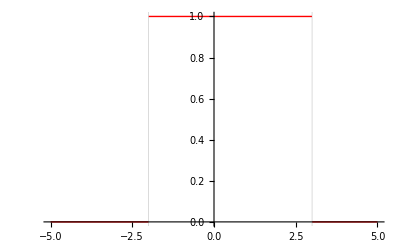

```mathematica
Plot[UnitStep[x+2]UnitStep[3-x],{x,-5,5},GridLines->{{-2,3},None},PlotStyle->{Red,Thick}]
```

```mathematica
ρ0[A_,B_,x_]:=UnitStep[x-A]UnitStep[B-x];
```

```mathematica
(* v < 0 *) Integrate[HeavisideTheta[-x],{x,ϵ,B},Assumptions->{ϵ∈Reals,B>ϵ}]
```

(-ϵ+B HeavisideTheta[-B]) HeavisideTheta[-ϵ]

```mathematica
(* v > 0 *)Integrate[HeavisideTheta[-x],{x,A,ϵ},Assumptions->{ϵ∈Reals,A<ϵ}]
```

HeavisideTheta[-A] (-A+ϵ HeavisideTheta[-ϵ])

```mathematica
Integrate[1/(1+Exp[x/kT]),{x,ϵ,B},Assumptions->{ϵ∈Reals,B>0,kT>0,B>ϵ}]
```

B-ϵ-kT Log[1+ⅇ^(B/kT)]+kT Log[1+ⅇ^(ϵ/kT)]

```mathematica
Integrate[1/(1+Exp[x/kT]),{x,A,ϵ},Assumptions->{ϵ∈Reals,kT>0,A<0}]
```

ConditionalExpression[-A+ϵ+kT Log[1+ⅇ^(A/kT)]-kT Log[1+ⅇ^(ϵ/kT)],A<ϵ]

Integrations from Γ_0 (reactant minimum) only

```mathematica
(* ϵ<Γ *)Integrate[ρ0[A,B,x]/(1+Exp[x/kT]),{x,ϵ,Γ},Assumptions->{Γ∈Reals,ϵ∈Reals,ϵ<Γ,kT>0,A<B,A<ϵ<B}]
```

B+HeavisideTheta[B-Γ] (-B+Γ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^(Γ/kT))])+kT Log[(1+ⅇ^(-ϵ/kT))/(1+ⅇ^(B/kT))]

```mathematica
(* ϵ>Γ *)Integrate[ρ0[A,B,x]/(1+Exp[x/kT]),{x,Γ,ϵ},Assumptions->{Γ∈Reals,ϵ∈Reals,ϵ>Γ,kT>0,A<B,A<ϵ<B}]
```

-A+ϵ+kT Log[1+ⅇ^(A/kT)]+HeavisideTheta[-A+Γ] (A-Γ-kT Log[1+ⅇ^(A/kT)]+kT Log[1+ⅇ^(Γ/kT)])-kT Log[1+ⅇ^(ϵ/kT)]

LDK integrations (with UnitStep and Fermi distributions)

```mathematica
Integrate[1/(1+Exp[β ϵ])Exp[-β(Γ-ϵ)^2/(4Λ)],{ϵ,-∞,∞},Assumptions->{β>0,λ>0,Γ∈Reals}]
```

$Aborted

```mathematica
Integrate[UnitStep[-ϵ]Exp[-β(Γ-ϵ)^2/(4Λ)],{ϵ,-∞,∞},Assumptions->{β>0,Λ>0,Γ∈Reals}]
```

√π √(Λ/β) Erfc[1/2 Γ √(β/Λ)]

```mathematica
Integrate[UnitStep[-ϵ]Exp[-β(Γ-ϵ)^2/(4Λ)],{ϵ,A,B},Assumptions->{A<B,β>0,Λ>0,Γ∈Reals}]
```

-√π √(Λ/β) UnitStep[-A] (Erf[1/2 (A-Γ) √(β/Λ)]+Erf[1/2 Γ √(β/Λ)]-(Erf[1/2 (B-Γ) √(β/Λ)]+Erf[1/2 Γ √(β/Λ)]) UnitStep[-B])

## Rate expressions

### General rate expression (all options):

```mathematica
kSC[T_,λ_,ΔG_,τL_]:=Module[{β,Γ},
Γ=ΔG+λ;
β=1/(kb T au2kcal);
1/τL(1-Abs[ΔG]^2/λ^2)√((β λ)/(16π))Exp[-β Γ^2/(4λ)]];
```

```mathematica
kLDK[T_,λ_,ΔG_,Δ_,OptionsPattern[{Distribution->"Fermi",Abottom->-∞,Btop->∞}]]:=Module[{A,B,dist,Γ,β,f,integral},
dist=OptionValue[Distribution];
A=OptionValue[Abottom];
B=OptionValue[Btop];
Γ=ΔG+λ;
β=1/(kb T au2kcal);
integral=Which[
dist=="Fermi",NIntegrate[1/(1+Exp[β ϵ])Exp[-β(Γ-ϵ)^2/(4λ)],{ϵ,A,B}],
dist=="Step",√((π λ)/β) UnitStep[-A] ((Erf[1/2 (B-Γ) √(β/λ)]+Erf[1/2 Γ √(β/λ)]) UnitStep[-B]-Erf[1/2 (A-Γ) √(β/λ)]-Erf[1/2 Γ √(β/λ)])
];
Δ/hbarkcalps √((π β)/λ)integral
];
```

```mathematica
kLZ[T_,λ_,ΔG_,Δ_,OptionsPattern[{Type->"Γ",Distribution->"Fermi",Abottom->-∞,Btop->∞,NAcorrection->False}]]:=Module[{type,nac,dist,β,Γ,f,P,M,ΞΓ0,ΞΓ0nac,Ξ80,ΞΓ,ΞΓnac,Ξ8,A,B,ΞAB,Ξ},
type=OptionValue[Type];
nac=OptionValue[NAcorrection];
dist=OptionValue[Distribution];
A=OptionValue[Abottom];
B=OptionValue[Btop];
Γ=ΔG+λ;
β=1/(kb T au2kcal);
f[ϵ_]:=Which[
dist=="Fermi",1/(1+Exp[β ϵ]),
dist=="Step",UnitStep[-ϵ]
];
M[v_]:=Exp[-β v^2/(4 Ω^2 λ)];
P[ϵ_]:=Exp[-β(Γ-ϵ)^2/(4λ)];
ΞΓ0[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[f[ϵ](-ϵ+Γ f[Γ])]],
UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[f[Γ](-Γ+ϵ f[ϵ])]]
];
ΞΓ[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[Γ-ϵ+1/β Log[f[Γ]/f[ϵ]]]],
UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[-Γ+ϵ+1/β Log[f[ϵ]/f[Γ]]]]
];
ΞAB[ϵ_,v_]:=If[v<0,Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[B-ϵ-1/β Log[f[ϵ]/f[B]]]],Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[-A+ϵ+1/β Log[f[ϵ]/f[A]]]]];
ΞΓ0nac[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2f[A](-A+ϵ f[ϵ])]],
0(*UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2f[ϵ](-ϵ+B f[B])]]*)
];
ΞΓnac[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2(-A+ϵ+1/β Log[f[ϵ]/f[A]])]],
0(*UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2(B-ϵ+1/β Log[f[B]/f[ϵ]])]]*)
];
Ξ[ϵ_,v_]:=Which[
type=="AB",ΞAB[ϵ,v],
type=="Γ"&&dist=="Step",ΞΓ0[ϵ,v]+If[nac,ΞΓ0nac[ϵ,v],0],
type=="Γ"&&dist=="Fermi",ΞΓ[ϵ,v]+If[nac,ΞΓnac[ϵ,v],0],
True,0
];
(β Δ)/(2hbarkcalps Ω λ)NIntegrate[f[ϵ]P[ϵ]NIntegrate[M[v]Ξ[ϵ,v],{v,-∞,∞},MinRecursion->4],{ϵ,A,B},MinRecursion->4]
];
```

```mathematica
kLDK[300,10,-11,0.00001,Distribution->"Fermi"]
```

0.00252087

### Rate constant for a single band:

Integrations from Γ_0 (reactant minimum) only

ϵ < Γ:

```mathematica
Integrate[ρ0[A,B,x]UnitStep[-x],{x,ϵ,Γ},Assumptions->{Γ∈Reals,ϵ∈Reals,ϵ<Γ,kT>0,A<B,A<ϵ<B}]
```

ConditionalExpression[0, ϵ>0]

```mathematica
Integrate[ρ0[A,B,x]/(1+Exp[x/kT]),{x,ϵ,Γ},Assumptions->{Γ∈Reals,ϵ∈Reals,ϵ<Γ,kT>0,A<B,A<ϵ<B}]
```

Integrate[ρ0[A,B,x]/(1+ⅇ^(x/kT)),{x,ϵ,Γ},Assumptions→{Γ∈ℝ,ϵ∈ℝ,ϵ<Γ,kT>0,A<B,A<ϵ<B}]

ϵ > Γ:

```mathematica
Integrate[ρ0[A,B,x]UnitStep[-x],{x,Γ,ϵ},Assumptions->{Γ∈Reals,ϵ∈Reals,ϵ>Γ,kT>0,A<B,A<ϵ<B}]
```

ConditionalExpression[0, ϵ>0]

```mathematica
(* ϵ>Γ *)Integrate[ρ0[A,B,x]/(1+Exp[x/kT]),{x,Γ,ϵ},Assumptions->{Γ∈Reals,ϵ∈Reals,ϵ>Γ,kT>0,A<B,A<ϵ<B}]
```

Integrate[ρ0[A,B,x]/(1+ⅇ^(x/kT)),{x,Γ,ϵ},Assumptions→{Γ∈ℝ,ϵ∈ℝ,ϵ>Γ,kT>0,A<B,A<ϵ<B}]

Recrossing corrections:

ϵ<Γ, v<0

```mathematica
Integrate[ρ0[A,B,x]UnitStep[-x],{x,A,ϵ},Assumptions->{ϵ∈Reals,kT>0,A<B,A<ϵ<B}]
```

ConditionalExpression[0, A>0]

```mathematica
Integrate[ρ0[A,B,x] 1/(1+Exp[β x]),{x,A,ϵ},Assumptions->{β>0,ϵ∈Reals,kT>0,A<B,A<ϵ<B}]
```

Integrate[ρ0[A,B,x]/(1+ⅇ^(x β)),{x,A,ϵ},Assumptions→{β>0,ϵ∈ℝ,kT>0,A<B,A<ϵ<B}]

ϵ>Γ, v>0

```mathematica
Integrate[ρ0[A,B,x]UnitStep[-x],{x,ϵ,B},Assumptions->{ϵ∈Reals,kT>0,A<B,A<ϵ<B}]
```

ConditionalExpression[0, ϵ>0]

```mathematica
Integrate[ρ0[A,B,x] 1/(1+Exp[β x]),{x,A,ϵ},Assumptions->{β>0,ϵ∈Reals,kT>0,A<B,A<ϵ<B}]
```

Integrate[ρ0[A,B,x]/(1+ⅇ^(x β)),{x,A,ϵ},Assumptions→{β>0,ϵ∈ℝ,kT>0,A<B,A<ϵ<B}]

```mathematica
kLZband[T_,λ_,ΔG_,Δ_,OptionsPattern[{Distribution->"Fermi",Abottom->-2ev2kcal,Btop->2ev2kcal,NAcorrection->False}]]:=Module[{type,nac,dist,β,Γ,f,P,M,ΞΓ0,ΞΓ0nac,ΞΓ,ΞΓnac,A,B,Ξ},
nac=OptionValue[NAcorrection];
dist=OptionValue[Distribution];
A=OptionValue[Abottom];
B=OptionValue[Btop];
Γ=ΔG+λ;
β=1/(kb T au2kcal);
f[ϵ_]:=Which[
dist=="Fermi",1/(1+Exp[β ϵ]),
dist=="Step",UnitStep[-ϵ]
];
M[v_]:=Exp[-β v^2/(4 Ω^2 λ)];
P[ϵ_]:=Exp[-β(Γ-ϵ)^2/(4λ)];
ΞΓ0[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[f[ϵ] (-(-B+ϵ+(B-Γ) f[Γ-B]) f[Γ]+(f[Γ]-1) ((-B+ϵ+B f[-B]) f[ϵ]+ϵ UnitStep[B,ϵ]))]],
UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[f[A] (-1+f[A-Γ]) (A-ϵ f[ϵ])+f[Γ] f[A-Γ] (-Γ+ϵ f[ϵ])]]
];
ΞΓ[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[-ϵ+B+UnitStep[B-Γ] (-B+Γ-1/β Log[f[B]/f[Γ]])+1/β Log[f[B]/f[ϵ]]]],
UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[ϵ-A+UnitStep[-A+Γ] (A-Γ-1/β Log[f[Γ]/f[A]])+1/β Log[f[ϵ]/f[A]]]]
];
ΞΓ0nac[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2UnitStep[-A] (-A+ϵ UnitStep[-ϵ])]],
0(*UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2 UnitStep[-ϵ](-ϵ+B UnitStep[-B])]]*)
];
ΞΓnac[ϵ_,v_]:=If[v<0,
UnitStep[Γ-ϵ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2(-A+ϵ+1/β Log[f[ϵ]/f[A]])]],
0(*UnitStep[ϵ-Γ]Exp[-(2π Δ)/(hbarkcalps Abs[v])Abs[2(B-ϵ+1/β Log[f[B]/f[ϵ]])]]*)
];
Ξ[ϵ_,v_]:=Which[
dist=="Step",ΞΓ0[ϵ,v]+If[nac,ΞΓ0nac[ϵ,v],0],
dist=="Fermi",ΞΓ[ϵ,v]+If[nac,ΞΓnac[ϵ,v],0],
True,0
];
(β Δ)/(2hbarkcalps Ω λ)NIntegrate[f[ϵ]P[ϵ]NIntegrate[M[v]Ξ[ϵ,v],{v,-∞,∞},MinRecursion->4],{ϵ,A,B},MinRecursion->4]
];
```

```mathematica
kLZband[300,10,-9,0.0001,Distribution->"Fermi"]
```

0.00801425

## Tables and Plots

### Table with Nonadiabatic and Adiabatic Limits of the rate constant (ps^-1):

```mathematica
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0=-11; (* Intrinsic bias in kcal/mol *)
Grid[{
{"ΔG + λ = "<>ToString[ΔG0+λ]<>" kcal/mol","1/2LDK","⟵ LZ ⟶",SpanFromLeft,"Ω/2π","TST","Ω/π","2×TST"},
{SpanFromAbove,SpanFromAbove,"Δ≪kT","Δ≫kT",SpanFromAbove},
{"Step Function",
1/2 kLDK[T,λ,ΔG0,0.0001,Distribution->"Step"],
kLZ[T,λ,ΔG0,0.0001,Type->"Γ",Distribution->"Step"],
kLZ[T,λ,ΔG0,500,Type->"Γ",Distribution->"Step"],
Ω/(2π),Ω/(2π)PΓ[T,λ,ΔG0,0],Ω/π,Ω/π PΓ[T,λ,ΔG0,0]},
{"Fermi Distribution",
1/2 kLDK[T,λ,ΔG0,0.0001,Distribution->"Fermi"],
kLZ[T,λ,ΔG0,0.0001,Type->"Γ",Distribution->"Fermi"],
kLZ[T,λ,ΔG0,500,Type->"Γ",Distribution->"Fermi"],
Ω/(2π),Ω/(2π)PΓ[T,λ,ΔG0,0],Ω/π,Ω/π PΓ[T,λ,ΔG0,0]}
},Frame->All,Background->{None,{LightPink,LightPink}},Alignment->{{Right},{Center,Center,Center}}]
```

ΔG + λ = -1 kcal/mol | 1/2LDK | ⟵ LZ ⟶ |  | Ω/2π | TST | Ω/π | 2×TST
 |  | Δ≪kT | Δ≫kT |  |  |  | 
Step Function | 0.0127069 | 0.0125825 | 4.61549 | 2.30775 | 2.21297 | 4.61549 | 4.42594
Fermi Distribution | 0.0126043 | 0.0124832 | 4.61549 | 2.30775 | 2.21297 | 4.61549 | 4.42594
Step Function (Γ_0→∞) | 0.0127069 | 0.0125439 | 2.21303 | 2.30775 | 2.21297 | 4.61549 | 4.42594
Fermi Distribution (Γ_0→∞) | 0.0126043 | 0.0124413 | 0.548861 | 2.30775 | 2.21297 | 4.61549 | 4.42594
Step Function (AB) | 0.0127069 | 0.0120356 | 1.25941×10^-7 | 2.30775 | 2.21297 | 4.61549 | 4.42594
Fermi Distribution (AB) | 0.0126043 | 0.0243805 | 0.548861 | 2.30775 | 2.21297 | 4.61549 | 4.42594

### Plots of a general rate constants (sp-band):

```mathematica
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0=-9; (* Intrinsic bias in kcal/mol *)
LZgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,10,0.5}]];
LDKgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}]];
Monitor[
LZStepList=Table[{Δ,kLZ[T,λ,ΔG0,Δ,Type->"Γ",Distribution->"Step"]},{Δ,LZgrid}],
Row[{"(1) LZ with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacStepList=Table[{Δ,kLZ[T,λ,ΔG0,Δ,Type->"Γ",Distribution->"Step",NAcorrection->True]},{Δ,LZgrid}],
Row[{"(1) LZ^(nac) with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZFermiList=Table[{Δ,kLZ[T,λ,ΔG0,Δ,Type->"Γ",Distribution->"Fermi"]},{Δ,LZgrid}],
Row[{"(2) LZ with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacFermiList=Table[{Δ,kLZ[T,λ,ΔG0,Δ,Type->"Γ",Distribution->"Fermi",NAcorrection->True]},{Δ,LZgrid}],
Row[{"(2) LZ^(nac) with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKStepList=Table[{Δ,kLDK[T,λ,ΔG0,Δ,Distribution->"Step"]},{Δ,LDKgrid}],
Row[{"(3) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKFermiList=Table[{Δ,kLDK[T,λ,ΔG0,Δ,Distribution->"Fermi"]},{Δ,LDKgrid}],
Row[{"(4) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Speak["Calculation is finished. Thank you."];
```

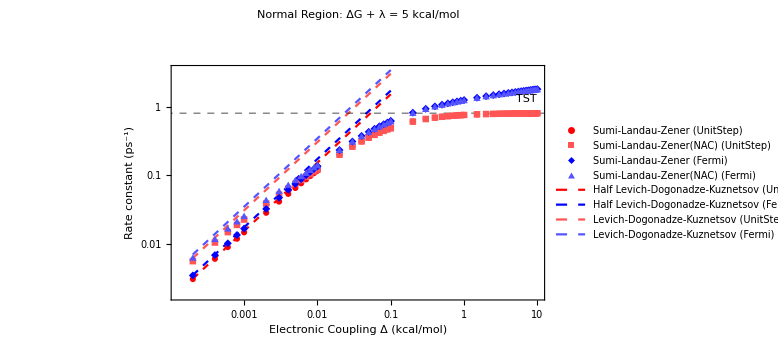

```mathematica
ListLogLogPlot[{
LZStepList,
LZnacStepList,
LZFermiList,
LZnacFermiList,
MapAt[#/2&,LDKStepList,{All,2}],
MapAt[#/2&,LDKFermiList,{All,2}],
LDKStepList,
LDKFermiList
},
GridLines->{None,{Ω/(2π)PΓ[T,λ,ΔG0,0],Ω/π}},
GridLinesStyle->Directive[Black,Dashed,Thin],
PlotLabel->If[ΔG0+λ<0,
Style["\nInverted Region: ΔG + λ = "<>ToString[ΔG0+λ]<>" kcal/mol",Black],
Style["\nNormal Region: ΔG + λ = "<>ToString[ΔG0+λ]<>" kcal/mol",Black]],
ImageSize->Large,Joined->{False,False,False,False,True,True,True,True},
PlotStyle->{Red,Lighter[Red],Blue,Lighter[Blue],{Red,Dashed},{Blue,Dashed},{Lighter[Red],Dashed},{Lighter[Blue],Dashed}},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,None,None,None,None},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"Sumi-Landau-Zener (UnitStep)",
"Sumi-Landau-Zener(NAC) (UnitStep)",
"Sumi-Landau-Zener (Fermi)",
"Sumi-Landau-Zener(NAC) (Fermi)",
"Half Levich-Dogonadze-Kuznetsov (UnitStep)",
"Half Levich-Dogonadze-Kuznetsov (Fermi)",
"Levich-Dogonadze-Kuznetsov (UnitStep)",
"Levich-Dogonadze-Kuznetsov (Fermi)"
},LegendFunction->Panel,LabelStyle->11,LegendLayout->"Column"],{0.7,0.2500}],
Epilog->{
Text["TST",{Log[7],Log[Ω/(2π)PΓ[T,λ,ΔG0,0]+0.5]}],
Text["Ω/π",{Log[7],Log[Ω/π+0.8]}],
Text["FGR/2",{Log[0.20],Log[Ω/π+2.5]}],
Text["FGR",{Log[0.04],Log[Ω/π+7]}]
},
FrameLabel->{"Electronic Coupling Δ (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

```mathematica
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0I=-11; (* Intrinsic bias in kcal/mol *)
LZgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,10,0.5}]];
LDKgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}]];
Monitor[
LZStepListI=Table[{Δ,kLZ[T,λ,ΔG0I,Δ,Type->"Γ",Distribution->"Step"]},{Δ,LZgrid}],
Row[{"(1) LZ with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacStepListI=Table[{Δ,kLZ[T,λ,ΔG0I,Δ,Type->"Γ",Distribution->"Step",NAcorrection->True]},{Δ,LZgrid}],
Row[{"(1) LZ^(nac) with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZFermiListI=Table[{Δ,kLZ[T,λ,ΔG0I,Δ,Type->"Γ",Distribution->"Fermi"]},{Δ,LZgrid}],
Row[{"(2) LZ with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacFermiListI=Table[{Δ,kLZ[T,λ,ΔG0I,Δ,Type->"Γ",Distribution->"Fermi",NAcorrection->True]},{Δ,LZgrid}],
Row[{"(2) LZ^(nac) with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKStepListI=Table[{Δ,kLDK[T,λ,ΔG0I,Δ,Distribution->"Step"]},{Δ,LDKgrid}],
Row[{"(3) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKFermiListI=Table[{Δ,kLDK[T,λ,ΔG0I,Δ,Distribution->"Fermi"]},{Δ,LDKgrid}],
Row[{"(4) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Speak["Calculation is finished. Thank you."];
```

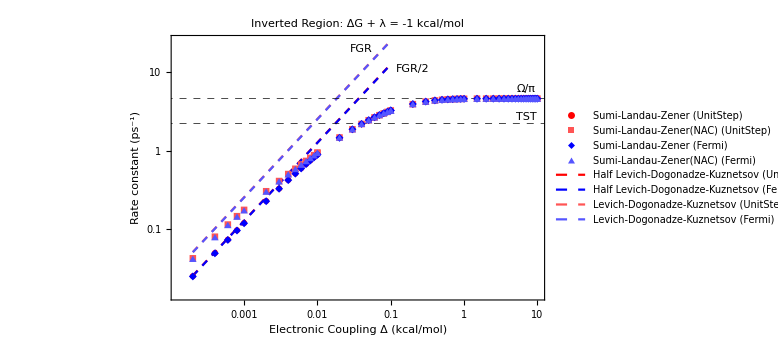

```mathematica
ListLogLogPlot[{
LZStepListI,
LZnacStepListI,
LZFermiListI,
LZnacFermiListI,
MapAt[#/2&,LDKStepListI,{All,2}],
MapAt[#/2&,LDKFermiListI,{All,2}],
LDKStepListI,
LDKFermiListI
},
GridLines->{None,{Ω/(2π)PΓ[T,λ,ΔG0I,0],Ω/π}},
GridLinesStyle->Directive[Black,Dashed,Thin],
PlotLabel->If[ΔG0I+λ<0,
Style["\nInverted Region: ΔG + λ = "<>ToString[ΔG0I+λ]<>" kcal/mol",Black],
Style["\nNormal Region: ΔG + λ = "<>ToString[ΔG0I+λ]<>" kcal/mol",Black]],
ImageSize->Large,Joined->{False,False,False,False,True,True,True,True},
PlotStyle->{Red,Lighter[Red],Blue,Lighter[Blue],{Red,Dashed},{Blue,Dashed},{Lighter[Red],Dashed},{Lighter[Blue],Dashed}},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,None,None,None,None},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"Sumi-Landau-Zener (UnitStep)",
"Sumi-Landau-Zener(NAC) (UnitStep)",
"Sumi-Landau-Zener (Fermi)",
"Sumi-Landau-Zener(NAC) (Fermi)",
"Half Levich-Dogonadze-Kuznetsov (UnitStep)",
"Half Levich-Dogonadze-Kuznetsov (Fermi)",
"Levich-Dogonadze-Kuznetsov (UnitStep)",
"Levich-Dogonadze-Kuznetsov (Fermi)"
},LegendFunction->Panel,LabelStyle->11],{0.7,0.25}],
Epilog->{
Text["TST",{Log[7],Log[Ω/(2π)PΓ[T,λ,ΔG0I,0]+0.5]}],
Text["Ω/π",{Log[7],Log[Ω/π+1.5]}],
Text["FGR/2",{Log[0.2],Log[Ω/π+6.5]}],
Text["FGR",{Log[0.04],Log[Ω/π+15]}]
},
FrameLabel->{"Electronic Coupling Δ (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

### Plots of rate constants for (filled) d-band only:

The d-band of bulk gold goes from (approximately) -150 kcal/mol to -30 kcal/mol (Fermi level is zero)
The d_(z^2)-band of gold surface should be much narrower.

```mathematica
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0=-9.5`10; (* Intrinsic bias in kcal/mol *)
dBottom=-100;
dTop=-0.25`10;
LZgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,10,0.5}]];
LDKgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}]];
Monitor[
LZStepList=Table[{Δ,kLZband[T,λ,ΔG0,Δ,Distribution->"Step",Abottom->dBottom,Btop->dTop]},{Δ,LZgrid}],
Row[{"(1) LZ with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacStepList=Table[{Δ,kLZband[T,λ,ΔG0,Δ,Distribution->"Step",Abottom->dBottom,Btop->dTop,NAcorrection->True]},{Δ,LZgrid}],
Row[{"(1) LZ^(nac) with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZFermiList=Table[{Δ,kLZband[T,λ,ΔG0,Δ,Distribution->"Fermi",Abottom->dBottom,Btop->dTop]},{Δ,LZgrid}],
Row[{"(2) LZ with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacFermiList=Table[{Δ,kLZband[T,λ,ΔG0,Δ,Distribution->"Fermi",Abottom->dBottom,Btop->dTop,NAcorrection->True]},{Δ,LZgrid}],
Row[{"(2) LZ^(nac) with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKStepList=Table[{Δ,kLDK[T,λ,ΔG0,Δ,Distribution->"Step",Abottom->dBottom,Btop->dTop]},{Δ,LDKgrid}],
Row[{"(3) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKFermiList=Table[{Δ,kLDK[T,λ,ΔG0,Δ,Distribution->"Fermi",Abottom->dBottom,Btop->dTop]},{Δ,LDKgrid}],
Row[{"(4) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Speak["Calculation is finished. Thank you."];
```

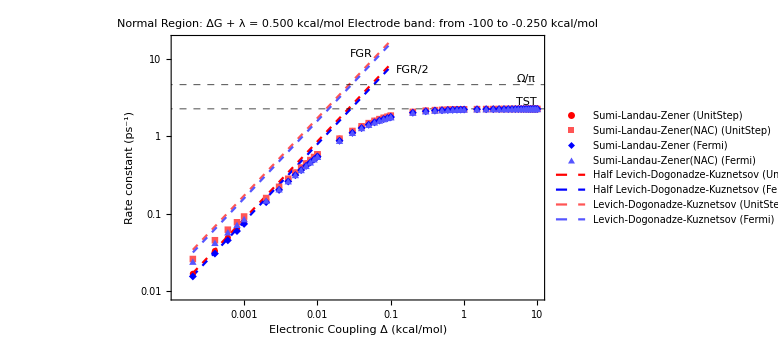

```mathematica
ListLogLogPlot[{
LZStepList,
LZnacStepList,
LZFermiList,
LZnacFermiList,
MapAt[#/2&,LDKStepList,{All,2}],
MapAt[#/2&,LDKFermiList,{All,2}],
LDKStepList,
LDKFermiList
},
GridLines->{None,{Ω/(2π)PΓ[T,λ,ΔG0,dTop],Ω/π}},
GridLinesStyle->Directive[Black,Dashed,Thin],
PlotLabel->
Column[{
If[ΔG0+λ<0,
Style["\nInverted Region: ΔG + λ = "<>ToString[NumberForm[ΔG0+λ,{4,3}]]<>" kcal/mol",Black],
Style["\nNormal Region: ΔG + λ = "<>ToString[NumberForm[ΔG0+λ,{4,3}]]<>" kcal/mol",Black]],
Style["Electrode band: from "<>ToString[NumberForm[dBottom,{4,3}]]<>" to "<>ToString[NumberForm[dTop,{4,3}],StandardForm]<> " kcal/mol",Black]
}],
ImageSize->Large,Joined->{False,False,False,False,True,True,True,True},
PlotStyle->{Red,Lighter[Red],Blue,Lighter[Blue],{Red,Dashed},{Blue,Dashed},{Lighter[Red],Dashed},{Lighter[Blue],Dashed}},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,None,None,None,None},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"Sumi-Landau-Zener (UnitStep)",
"Sumi-Landau-Zener(NAC) (UnitStep)",
"Sumi-Landau-Zener (Fermi)",
"Sumi-Landau-Zener(NAC) (Fermi)",
"Half Levich-Dogonadze-Kuznetsov (UnitStep)",
"Half Levich-Dogonadze-Kuznetsov (Fermi)",
"Levich-Dogonadze-Kuznetsov (UnitStep)",
"Levich-Dogonadze-Kuznetsov (Fermi)"
},LegendFunction->Panel,LabelStyle->11,LegendLayout->"Column"],Right],
Epilog->{
Text["TST",{Log[7],Log[Ω/(2π)PΓ[T,λ,ΔG0,0]+0.5]}],
Text["Ω/π",{Log[7],Log[Ω/π+0.8]}],
Text["FGR/2",{Log[0.20],Log[Ω/π+2.5]}],
Text["FGR",{Log[0.04],Log[Ω/π+7]}]
},
FrameLabel->{"Electronic Coupling Δ (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

```mathematica
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0I=-10.5; (* Intrinsic bias in kcal/mol *)
dBottom=-100;
dTop=-0.25;
LZgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,10,0.5}]];
LDKgrid=Union[Table[x,{x,0,0.001,0.0002}],Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}]];
Monitor[
LZStepListI=Table[{Δ,kLZband[T,λ,ΔG0I,Δ,Distribution->"Step",Abottom->dBottom,Btop->dTop]},{Δ,LZgrid}],
Row[{"(1) LZ with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacStepListI=Table[{Δ,kLZband[T,λ,ΔG0I,Δ,Distribution->"Step",Abottom->dBottom,Btop->dTop,NAcorrection->True]},{Δ,LZgrid}],
Row[{"(1) LZ^(nac) with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZFermiListI=Table[{Δ,kLZband[T,λ,ΔG0I,Δ,Distribution->"Fermi",Abottom->dBottom,Btop->dTop]},{Δ,LZgrid}],
Row[{"(2) LZ with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LZnacFermiListI=Table[{Δ,kLZband[T,λ,ΔG0I,Δ,Distribution->"Fermi",Abottom->dBottom,Btop->dTop,NAcorrection->True]},{Δ,LZgrid}],
Row[{"(2) LZ^(nac) with Fermi distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKStepListI=Table[{Δ,kLDK[T,λ,ΔG0I,Δ,Distribution->"Step",Abottom->dBottom,Btop->dTop]},{Δ,LDKgrid}],
Row[{"(3) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
LDKFermiListI=Table[{Δ,kLDK[T,λ,ΔG0I,Δ,Distribution->"Fermi",Abottom->dBottom,Btop->dTop]},{Δ,LDKgrid}],
Row[{"(4) FGR with Unit Step distribution: Δ = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
Speak["Calculation is finished. Thank you."];
EmitSound[Sound[{
SoundNote["E",1.0,"RockOrgan"],
SoundNote["D",0.5,"RockOrgan"],
SoundNote["E",1.0,"RockOrgan"],
SoundNote["G",1.0,"RockOrgan"],
SoundNote["E",1.0,"RockOrgan"],
SoundNote["D",0.5,"RockOrgan"],
SoundNote["E",0.5,"RockOrgan"]
}]];
```

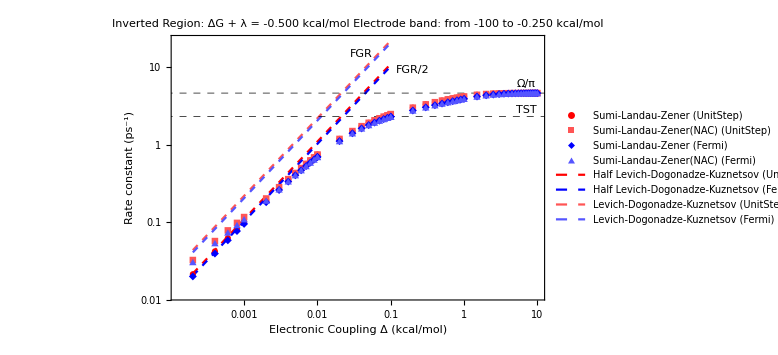

```mathematica
ListLogLogPlot[{
LZStepListI,
LZnacStepListI,
LZFermiListI,
LZnacFermiListI,
MapAt[#/2&,LDKStepListI,{All,2}],
MapAt[#/2&,LDKFermiListI,{All,2}],
LDKStepListI,
LDKFermiListI
},
GridLines->{None,{Ω/(2π)PΓ[T,λ,ΔG0I,dTop],Ω/π}},
GridLinesStyle->Directive[Black,Dashed,Thin],
PlotLabel->
Column[{
If[ΔG0I+λ<0,
Style["\nInverted Region: ΔG + λ = "<>ToString[NumberForm[ΔG0I+λ,{4,3}]]<>" kcal/mol",Black],
Style["\nNormal Region: ΔG + λ = "<>ToString[NumberForm[ΔG0I+λ,{4,3}]]<>" kcal/mol",Black]],
Style["Electrode band: from "<>ToString[dBottom]<>" to "<>ToString[NumberForm[dTop,{4,3}],StandardForm]<> " kcal/mol",Black]
}],
ImageSize->Large,Joined->{False,False,False,False,True,True,True,True},
PlotStyle->{Red,Lighter[Red],Blue,Lighter[Blue],{Red,Dashed},{Blue,Dashed},{Lighter[Red],Dashed},{Lighter[Blue],Dashed}},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,None,None,None,None},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"Sumi-Landau-Zener (UnitStep)",
"Sumi-Landau-Zener(NAC) (UnitStep)",
"Sumi-Landau-Zener (Fermi)",
"Sumi-Landau-Zener(NAC) (Fermi)",
"Half Levich-Dogonadze-Kuznetsov (UnitStep)",
"Half Levich-Dogonadze-Kuznetsov (Fermi)",
"Levich-Dogonadze-Kuznetsov (UnitStep)",
"Levich-Dogonadze-Kuznetsov (Fermi)"
},LegendFunction->Panel,LabelStyle->11],Right],
Epilog->{
Text["TST",{Log[7],Log[Ω/(2π)PΓ[T,λ,ΔG0I,0]+0.5]}],
Text["Ω/π",{Log[7],Log[Ω/π+1.5]}],
Text["FGR/2",{Log[0.2],Log[Ω/π+4.5]}],
Text["FGR",{Log[0.04],Log[Ω/π+10]}]
},
FrameLabel->{"Electronic Coupling Δ (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

## Vibrational Overlaps

## Morse potentials for D-H (reactant) and A-H (product) bonds: U^Morse(q)=(D(1-e^(-β (q-q_0))))^2

### Morse parameters (1 - Tyrosine-OH; 2 - Phosphate-OH/Imidazole-NH)

```mathematica
βMorse[ω_,D_,μ_]:=ω cm2au √((μ Dalton)/(2D kcal2au));
```

#### Parameters for the Proton Donor (Donor-H Morse potential)

```mathematica
Row[{
Highlighted[Style["Choose proton donor:",Black]],
Button["Proton donor: Water (alkaline conditions)",
donor="Water";
RDH=0.976;
D1=119 kcal2au;
ω1=3450;
β1=βMorse[ω1,D1 au2kcal,MassH];
λ1=SetAccuracy[(√(2μH D1))/(β1 ℏ),AccN];
λ1D=SetAccuracy[(√(2μD D1))/(β1 ℏ),AccN]],
Button["Proton donor: Hydronium (acidic conditions)",
donor="Hydronium";
RDH=0.967;
D1=142.5 kcal2au;
ω1=3200;
β1=βMorse[ω1,D1 au2kcal,MassH];
λ1=SetAccuracy[(√(2μH D1))/(β1 ℏ),AccN];
λ1D=SetAccuracy[(√(2μD D1))/(β1 ℏ),AccN]]
}]
Grid[{
{"Proton donor group",Dynamic[donor]},
{"Morse potential parameters",SpanFromLeft},
{"Proton vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β1 √((2D1)/μH),{7,3}]]},
{"Deuteron vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β1 √((2D1)/μD),{7,3}]]},
{"Morse β parameter, Å^-1",Dynamic[NumberForm[β1/bohr2a,{7,3}]]},
{"Equilibrium bond length, Å",Dynamic[RDH]}
},Frame->All,Alignment->{{Left,"."}},Background->{None,{Pink,LightGray}}
]
```

Choose proton donor:Proton donor: Water (alkaline conditions)Proton donor: Hydronium (acidic conditions)

Proton donor group | 
Morse potential parameters | 
Proton vibrational frequency, cm^-1 | 
Deuteron vibrational frequency, cm^-1 | 
Morse β parameter, Å^-1 | 
Equilibrium bond length, Å |

#### Acceptor: site on the electrode surface

```mathematica
Row[
{Highlighted[Style["Choose proton acceptor:",Black]],
Button[Style["Au[111]",Blue],
acceptor="Au[111]";
RAH=1.6;
D2=52 kcal2au;
ω2=1880;
β2=βMorse[ω2,D2 au2kcal,MassH];
λ2=SetAccuracy[(√(2μH D2))/(β2 ℏ),AccN];
λ2D=SetAccuracy[(√(2μD D2))/(β2 ℏ),AccN],
Appearance->{"DialogBox"}],
Button[Style["Au[100]",Red],
acceptor="Au[100]";
RAH=1.009;
D2=93.9 kcal2au;
ω2=3376;
β2=βMorse[ω2,D2 au2kcal,MassH];
λ2=SetAccuracy[(√(2μH D2))/(β2 ℏ),AccN];
λ2D=SetAccuracy[(√(2μD D2))/(β2 ℏ),AccN],
Appearance->{"DialogBox"}]
}
]
Grid[{
{"Proton acceptor site",Dynamic[acceptor]},
{"Morse potential parameters",SpanFromLeft},
{"Proton vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β2 √((2D2)/μH),{7,3}]]},
{"Deuteron vibrational frequency, cm^-1",Dynamic[NumberForm[au2cm β2 √((2D2)/μD),{7,3}]]},
{"Morse β parameter, Å^-1",Dynamic[NumberForm[β2/bohr2a,{7,3}]]},
{"Equilibrium bond length, Å",Dynamic[RAH]}
},
Frame->All,Alignment->{{Left,Right}},
Background->{None,{Pink,LightGray,None,None,None,None,LightGray,None,None,LightGray,None,None,LightGray}}
]
```

Choose proton acceptor:Au[111]Au[100]

Proton acceptor site | 
Morse potential parameters | 
Proton vibrational frequency, cm^-1 | 
Deuteron vibrational frequency, cm^-1 | 
Morse β parameter, Å^-1 | 
Equilibrium bond length, Å |

#### R0 - Distance (in Bohr) between the minima of reactant and product proton potentials; RDA - Donor-acceptor distance in Å.

```mathematica
R0[RDA_]:=(RDA-RDH-RAH)a2bohr;
RDA[R_]:=R bohr2a+RDH+RAH;
```

## Analytical expressions for the Morse wavefunctions from [J. P. Dahl, M. Springborg, J. Chem. Phys. 88, 4535 (1987)] (typo in Eq.(38): factor √α is missing)

```mathematica
ξ1[x_]:=SetAccuracy[2λ1 Exp[-β1 x],AccN];
ξ1D[x_]:=SetAccuracy[2λ1D Exp[-β1 x],AccN];
ξ2[x_]:=SetAccuracy[2λ2 Exp[-β2 x],AccN];
ξ2D[x_]:=SetAccuracy[2λ2D Exp[-β2 x],AccN];
```

Energies (Hartrees):

```mathematica
E1[n_]:=SetAccuracy[((n+1/2)-1/(2λ1)(n+1/2)^2)ℏ √((2D1 β1^2)/μH),AccN];
E1D[n_]:=SetAccuracy[((n+1/2)-1/(2λ1D)(n+1/2)^2)ℏ √((2D1 β1^2)/μD),AccN];
E2[n_]:=SetAccuracy[((n+1/2)-1/(2λ2)(n+1/2)^2)ℏ √((2D2 β2^2)/μH),AccN];
E2D[n_]:=SetAccuracy[((n+1/2)-1/(2λ2D)(n+1/2)^2)ℏ √((2D2 β2^2)/μD),AccN];
```

Normalization factors:

```mathematica
N1D[n_]:=SetAccuracy[√((β1(2λ1D-2n-1)Gamma[n+1])/Gamma[2λ1D-n]),AccN];
N2D[n_]:=SetAccuracy[√((β2(2λ2D-2n-1)Gamma[n+1])/Gamma[2λ2D-n]),AccN];
N1[n_]:=SetAccuracy[√((β1(2λ1-2n-1)Gamma[n+1])/Gamma[2λ1-n]),AccN];
N2[n_]:=SetAccuracy[√((β2(2λ2-2n-1)Gamma[n+1])/Gamma[2λ2-n]),AccN];
```

```mathematica
β2
```

0.901615542314112293498409786812999525260347457585723951742732883414870040357452828919003262861702343306

Wavefunctions:

```mathematica
ϕ1[x_,n_]:=SetAccuracy[N1[n]Exp[-ξ1[x]/2] ξ1[x]^(λ1-n-1/2)LaguerreL[n,2λ1-2n-1,ξ1[x]],AccN];
ϕ1D[x_,n_]:=SetAccuracy[N1D[n]Exp[-ξ1D[x]/2] ξ1D[x]^(λ1D-n-1/2)LaguerreL[n,2λ1D-2n-1,ξ1D[x]],AccN];
ϕ2[x_,n_]:=SetAccuracy[N2[n]Exp[-ξ2[x]/2] ξ2[x]^(λ2-n-1/2)LaguerreL[n,2λ2-2n-1,ξ2[x]],AccN];
ϕ2D[x_,n_]:=SetAccuracy[N2D[n]Exp[-ξ2D[x]/2] ξ2D[x]^(λ2D-n-1/2)LaguerreL[n,2λ2D-2n-1,ξ2D[x]],AccN];
```

Number of bound states:

```mathematica
Nbound1=IntegerPart[λ1-1/2];
Nbound2=IntegerPart[λ2-1/2];
Nbound1D=IntegerPart[λ1D-1/2];
Nbound2D=IntegerPart[λ2D-1/2];
```

```mathematica
Min[Nbound1,Nbound2,Nbound1D,Nbound2D]
```

18

## Morse overlap integrals in terms of the Wigner function based on [J. C. Lopez, A. L. Rivera, Yu. F. Smirnov, A. Frank, arXiv:physics/0109017v]

General case:

```mathematica
FCH[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`100;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],
{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

```mathematica
FCD[R_,nu1_,nu2_]:=
Module[{AccN,Acc,l1,l2,j1, beta1, j2, beta2,y1,y2,a,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,peak,xatmax,fatmax,integr,res,finteg2,smallestx,x,X},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FCH[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Accuracies: *)
Acc=15;
AccN=60;
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta1=SetAccuracy[β1,AccN];
beta2=SetAccuracy[β2,AccN];
a=SetAccuracy[beta2/beta1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta1*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta2*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[a*FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta1*R*(l1)/2]*Exp[-beta2*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
(* ===========================================================*)
(* Integration Section *)
(* Integral Ia.Calculation with scaling *)
(* ===========================================================*)Lambda=SetAccuracy[j1-nu1+l1-a*(j2-nu2+l2),AccN];
(* Integrand *)
integr=SetAccuracy[x^(Lambda-1)*Exp[-(y1*x+y2*x^(-a))/2],AccN];
finteg[xx_]:=xx^(Lambda-1)*Exp[-(y1*xx+y2*xx^(-a))/2];
(* Find smallest x before underflow occurs *)
Off[General::"unfl"];
smallestx=0.1`50;
While[finteg[smallestx]>$MinNumber,smallestx=smallestx/2];
smallestx=smallestx*2;
On[General::unfl];
(*Looking for position of maximum*)
aux=FindMaximum[integr,{x,smallestx+1,smallestx,∞},WorkingPrecision->AccN];
peak=aux[[2]][[1]][[2]];
xatmax=SetAccuracy[peak,AccN];
(*Integrand value at maximum*)
fatmax=SetAccuracy[finteg[peak],AccN];
finteg2=SetAccuracy[(1/fatmax)*(X*xatmax)^(Lambda-1)*Exp[-(y1*(X*xatmax)+y2*(X*xatmax)^(-a))/2],AccN];
res=SetAccuracy[fatmax*xatmax*NIntegrate[finteg2,{X,0,Infinity},PrecisionGoal->Acc,AccuracyGoal->Acc,Method->"DoubleExponential"],AccN];
(*Adding terms*)
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
(*Output*)
Re@Fcsum
];
```

Case β_1=β_2:

```mathematica
FC0H[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)
(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCH instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1-1/2,AccN];
j2=SetAccuracy[λ2-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

```mathematica
FC0D[R_,nu1_,nu2_]:=
Module[{l1,l2,j1, beta, j2, y1,y2,Fcsum,fac0a,fac0b,fac0,fac1a,fac1b,fac1,fac2,fac3,Fcaux,Lambda,aux,res},
(*-----------------------------------------------------------------------*)(* This program computes the Franck-Condon factor of two Morse functions *)
(* for the mirrored potentials for the case when Subscript[β, 1]=Subscript[β, 2]=β *)
(* Modified version of Lopez-Rivera-Smirnov-Frank *)
(* Usage: *)
(* FC0H[R,nu1,nu2] *)
(*---------------------------------------------------------------------*)(* Abort if Subscript[β, 1]≠Subscript[β, 2] *)
If[β1≠β2,(Print["β1≠β2: Use FCD instead..."];Abort[])];
(* Accuracies: *)
j1=SetAccuracy[λ1D-1/2,AccN];
j2=SetAccuracy[λ2D-1/2,AccN];
beta=SetAccuracy[β1,AccN];
y1=SetAccuracy[(2*j1+1)*Exp[-beta*R/2],AccN];
y2=SetAccuracy[(2*j2+1)*Exp[-beta*R/2],AccN];
Fcsum=0;
fac0a=SetAccuracy[2*Sqrt[FullSimplify[nu1!*(j1-nu1)*nu2!*(j2-nu2)/(Gamma[2*j1-nu1+1]*Gamma[2*j2-nu2+1])]],AccN];
fac0b=SetAccuracy[y1^(j1-nu1)*y2^(j2-nu2),AccN];
fac0=fac0a*fac0b;
Do[(*Do loops for summations*)
fac1a=SetAccuracy[(2*j1+1)^(l1)*(2*j2+1)^(l2),AccN];
fac1b=SetAccuracy[Exp[-beta*R*(l1)/2]*Exp[-beta*R*(l2)/2],AccN];
fac1=SetAccuracy[fac1a*fac1b,AccN];
fac2=SetAccuracy[(-1)^(l1+l2)/(l1!*l2!),AccN];
fac3=SetAccuracy[FullSimplify[Binomial[2*j1-nu1,nu1-l1]*Binomial[2*j2-nu2,nu2-l2]],AccN];
Fcaux=SetAccuracy[fac0*fac1*fac2*fac3,AccN];
Lambda=SetAccuracy[j1-nu1+l1-(j2-nu2+l2),AccN];
res=SetAccuracy[2(y2/y1)^(Lambda/2)BesselK[-Lambda,√(y1*y2)],AccN];
Fcsum=Fcsum+SetAccuracy[Fcaux*res,AccN],{l1,0,nu1},{l2,0,nu2}];
Fcsum];
```

## Morse overlap integrals and their distance dependence

### Numerical overlap integrals

```mathematica
SH[R_,i_,j_]:=Module[{x,integrand},
integrand=SetAccuracy[ϕ1[x,i]ϕ2[-x+R,j],AccN];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False,WorkingPrecision->50,AccuracyGoal->30]];
```

```mathematica
SD[R_,i_,j_]:=Module[{x,integrand},
integrand=SetAccuracy[ϕ1D[x,i]ϕ2D[-x+R,j],AccN];
NIntegrate[integrand,{x,-∞,∞},Method->{"DoubleExponential","SymbolicProcessing"->0},Compiled->False,WorkingPrecision->50,AccuracyGoal->30]];
```

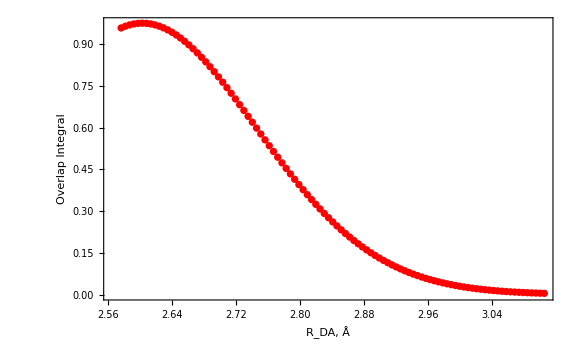

```mathematica
ListPlot[
Table[{RDA[x],SD[x,0,0]},{x,0,1,0.01}],
Axes->False,Frame->True,
FrameLabel->{"R_DA, Å","Overlap Integral"},
PlotStyle->{Black,Red},
PlotRange->All,ImageSize->Large
]
```

### Spline all the distance dependencies

```mathematica
Clear[SHs,SHtable,SDs,SDtable];
Nbound=10;
Array[SHs,{Nbound+1,Nbound+1},{0,0}];
Array[SHtable,{Nbound+1,Nbound+1},{0,0}];
Array[SDs,{Nbound+1,Nbound+1},{0,0}];
Array[SDtable,{Nbound+1,Nbound+1},{0,0}];
```

### (! MUST BE REEVALUATED UPON CHANGING THE PROTON ACCEPTOR : CLICK ON THE BUTTON BELOW!)

```mathematica
Button[Style["Spline overlap integrals",Red],
progress="Calculating and splining proton overlaps: ";
Monitor[
Do[
SHtable[i,j]=ParallelTable[{Ri,SH[Ri,i,j]},{Ri,-2.0,4.0,0.01}];
SHs[i,j]=Interpolation[SHtable[i,j],Method->"Spline",InterpolationOrder->3],
{i,0,Nbound},{j,0,Nbound}
],
Row[{"Proton overlaps: <",i,"|",j,">"},Frame->True,Background->Yellow,RoundingRadius->5]
];
Monitor[
Do[
SDtable[i,j]=ParallelTable[{Ri,SD[Ri,i,j]},{Ri,-2.0,4.0,0.01}];
SDs[i,j]=Interpolation[SDtable[i,j],Method->"Spline",InterpolationOrder->3],
{i,0,Nbound},{j,0,Nbound}
],
Row[{"Deuteron overlaps: <",i,"|",j,">"},Frame->True,Background->Yellow,RoundingRadius->5]
],
Appearance->{"DialogBox"},Method->"Queued"
]
```

Spline overlap integrals

```mathematica
Manipulate[
ListPlot[
{Table[{RDA[x],SH[x,μ,ν]},{x,-2.,4.,0.025}],
Table[{RDA[x],SHs[μ,ν][x]},{x,-2.,4.,0.025}],
Table[{RDA[x],SD[x,μ,ν]},{x,-2.,4.,0.025}],
Table[{RDA[x],SDs[μ,ν][x]},{x,-2.,4.,0.025}]},
Axes->False,Frame->True,
FrameLabel->{"R_DA, Å","Overlap Integral"},
PlotStyle->{Red,Red,Blue,Blue},Joined->{False,True,False,True},
PlotRange->All,ImageSize->Large,
PlotLegends->Placed[LineLegend[{
"Numerical Overlap Integral (Hydrogen)",
"Splined Overlap Integral (Hydrogen)",
"Numerical Overlap Integral (Deuterium)",
"Splined Overlap Integral (Deuterium)"
},LegendFunction->"Frame",LabelStyle->12,LegendLayout->"Column"],Above]
],
{{μ,0,"Reactant quantum number"},Table[k,{k,0,Nbound}]},
{{ν,0,"Product quantum number"},Table[k,{k,0,Nbound}]},
ControlType->Setter
]
```

```mathematica
RDA[-2.0]
```

1.51765

## Proton-Coupled Electron Transfer (Volmer reaction)

## Rate constant expressions for Volmer PCET

### Solvent-control limit (Zusman)

Zusman, L. D. Outer-Sphere Electron Transfer Reactions at an Electrode. Chemical Physics 1987, 112, 53–59.
https://doi.org/10.1016/0301-0104(87)85021-8

```mathematica
kSCvibZusman[T_,λ_,ΔG_,τL_,μmax_,
OptionsPattern[{ElBand->{-200,200},Isotope->"H"}]]:=Module[{A,B,isotope,Z,pμ,ϵμ,β,Γ,Γμ,ΔGμ,kμ,rate},
A=OptionValue[ElBand]⟦1⟧;
B=OptionValue[ElBand]⟦2⟧;
isotope=OptionValue[Isotope];
Γ=ΔG+λ;
β=1/(kb T au2kcal);

Z=Which[
isotope=="H",Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
rate=0;
Do[
ϵμ=Which[
isotope=="H",( E1[μ]-E1[0])au2kcal,
isotope=="D",( E1D[μ]-E1D[0])au2kcal
];
pμ=Exp[-β ϵμ]/Z;
Γμ=Γ-ϵμ-Min[0,B];
kμ=If[Γμ>0,1/τL √((β λ)/π^3)Exp[-β Γμ^2/(4λ)],2/τL];
rate+=pμ kμ,
{μ,0,μmax}];
rate
];
```

### Non-adiabatic limit (LDK with vibronic couplings)

```mathematica
kLDKvib[T_,λ_,ΔG_,V_,R_,μmax_,νmax_,
OptionsPattern[{
Distribution->"Fermi",
StatesPerAtom->1,
Abottom->-200,
Btop->200,
Isotope->"H"}]]:=Module[
{isotope,ns,A,B,dist,Γ,Γμν,β,f,wμ,Sμν,ϵμ,ϵν,integral,Z,sum},
isotope=OptionValue[Isotope];
dist=OptionValue[Distribution];
ns=OptionValue[StatesPerAtom];
A=OptionValue[Abottom];
B=OptionValue[Btop];
Γ=ΔG+λ;
β=1/(kb T au2kcal);
Z=Which[
isotope=="H",Sum[Exp[-β( E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
sum=0;
Do[
ϵμ=Which[
isotope=="H",( E1[μ]-E1[0])au2kcal,
isotope=="D",( E1D[μ]-E1D[0])au2kcal
];
ϵν=Which[
isotope=="H",( E2[ν]-E2[0])au2kcal,
isotope=="D",( E2D[ν]-E2D[0])au2kcal
];
wμ=Exp[-β ϵμ]/Z;
Γμν=Γ+ϵν-ϵμ;
Sμν=Which[
isotope=="H",SHs[μ,ν][R0[R]],
isotope=="D",SDs[μ,ν][R0[R]]
];
integral=Which[
dist=="Fermi",ns/(B-A)NIntegrate[1/(1+Exp[β ϵ])Exp[-β(Γμν-ϵ)^2/(4λ)],{ϵ,A,B}],
dist=="Step",ns/(B-A)√((π λ)/β)(Erf[1/2 √(β/λ)(B-Γμν)]-Erf[1/2 √(β/λ)(A-Γμν)]) 
];
sum+=wμ Sμν^2 integral,
{ν,0,νmax},{μ,0,μmax}];
V^2/hbarkcalps √((π β)/λ)sum
];
```

```mathematica
kLDKvib[300,10,-9,1,2.5,0,0,Distribution->"Fermi",Isotope->"H"]
```

0.240579

### General LZ expression for vibronic states with couplings ⟨aμ|H|kν⟩ = V_k ⟨μ|ν⟩

#### Integrations from Γ_0 (reactant minimum) for shifted Fermi distribution and density of states (for PCET)

```mathematica
ρθ[x_,A_,B_]:=HeavisideTheta[x-A]HeavisideTheta[B-x];
ρU[x_,A_,B_]:=UnitStep[x-A]UnitStep[B-x];
```

With Fermi distribution:

```mathematica
Intθ=Integrate[ρθ[x+δ,A,B]/(1+Exp[(x+δ)/kT]),{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
IntU=Integrate[ρU[x+δ,A,B]/(1+Exp[(x+δ)/kT]),{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

HeavisideTheta[-Γ+ϵ] HeavisideTheta[-A+δ+ϵ] (-(-1+HeavisideTheta[-A+Γ+δ]) (HeavisideTheta[A-δ-ϵ] HeavisideTheta[B-δ-ϵ] (A+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(A/kT))])+HeavisideTheta[-A+δ+ϵ] (A+kT Log[(1+ⅇ^(-B/kT))/(1+ⅇ^(A/kT))]+kT HeavisideTheta[B-δ-ϵ] Log[(ⅇ^(B/kT) (1+ⅇ^(-(δ+ϵ)/kT)))/(1+ⅇ^(B/kT))]))+HeavisideTheta[-A+Γ+δ] (HeavisideTheta[B-Γ-δ] HeavisideTheta[-Γ+ϵ] (-B+kT Log[(ⅇ^((Γ+δ)/kT) (1+ⅇ^(B/kT)))/(1+ⅇ^((Γ+δ)/kT))]+HeavisideTheta[B-δ-ϵ] (B-δ-ϵ-kT Log[1+ⅇ^(B/kT)]+kT Log[1+ⅇ^((δ+ϵ)/kT)]))+HeavisideTheta[Γ-ϵ] HeavisideTheta[B-δ-ϵ] (-(-1+HeavisideTheta[B-Γ-δ]) (B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))])+HeavisideTheta[B-Γ-δ] (Γ+kT Log[(ⅇ^(-ϵ/kT) (1+ⅇ^((δ+ϵ)/kT)))/(1+ⅇ^((Γ+δ)/kT))]))))+HeavisideTheta[-A+Γ+δ] HeavisideTheta[Γ-ϵ] (-(-1+HeavisideTheta[-A+δ+ϵ]) (HeavisideTheta[-A+Γ+δ] (-A+kT Log[(ⅇ^(B/kT) (1+ⅇ^(A/kT)))/(1+ⅇ^(B/kT))]+kT HeavisideTheta[B-Γ-δ] Log[(ⅇ^(-B/kT) (1+ⅇ^(B/kT)))/(1+ⅇ^(-(Γ+δ)/kT))])+HeavisideTheta[A-Γ-δ] HeavisideTheta[B-Γ-δ] (-A+kT Log[(ⅇ^((Γ+δ)/kT) (1+ⅇ^(A/kT)))/(1+ⅇ^((Γ+δ)/kT))]))+HeavisideTheta[-A+δ+ϵ] (HeavisideTheta[B-Γ-δ] HeavisideTheta[-Γ+ϵ] (-B+kT Log[(ⅇ^((Γ+δ)/kT) (1+ⅇ^(B/kT)))/(1+ⅇ^((Γ+δ)/kT))]+HeavisideTheta[B-δ-ϵ] (B-δ-ϵ-kT Log[1+ⅇ^(B/kT)]+kT Log[1+ⅇ^((δ+ϵ)/kT)]))+HeavisideTheta[Γ-ϵ] HeavisideTheta[B-δ-ϵ] (-(-1+HeavisideTheta[B-Γ-δ]) (B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))])+HeavisideTheta[B-Γ-δ] (Γ+kT Log[(ⅇ^(-ϵ/kT) (1+ⅇ^((δ+ϵ)/kT)))/(1+ⅇ^((Γ+δ)/kT))]))))

UnitStep[-A+Γ+δ] UnitStep[Γ-ϵ] (-((-A+kT Log[(ⅇ^((Γ+δ)/kT) (1+ⅇ^(A/kT)))/(1+ⅇ^((Γ+δ)/kT))]) UnitStep[A-Γ-δ] UnitStep[B-Γ-δ]+(-A+kT Log[(ⅇ^(B/kT) (1+ⅇ^(A/kT)))/(1+ⅇ^(B/kT))]+kT Log[(ⅇ^(-B/kT) (1+ⅇ^(B/kT)))/(1+ⅇ^(-(Γ+δ)/kT))] UnitStep[B-Γ-δ]) UnitStep[-A+Γ+δ]) (-1+UnitStep[-A+δ+ϵ])+((-(B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))]) (-1+UnitStep[B-Γ-δ])+(Γ+kT Log[(ⅇ^(-ϵ/kT) (1+ⅇ^((δ+ϵ)/kT)))/(1+ⅇ^((Γ+δ)/kT))]) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+kT Log[(ⅇ^((Γ+δ)/kT) (1+ⅇ^(B/kT)))/(1+ⅇ^((Γ+δ)/kT))]+(B-δ-ϵ-kT Log[1+ⅇ^(B/kT)]+kT Log[1+ⅇ^((δ+ϵ)/kT)]) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ]) UnitStep[-A+δ+ϵ])+UnitStep[-Γ+ϵ] UnitStep[-A+δ+ϵ] (UnitStep[-A+Γ+δ] ((-(B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))]) (-1+UnitStep[B-Γ-δ])+(Γ+kT Log[(ⅇ^(-ϵ/kT) (1+ⅇ^((δ+ϵ)/kT)))/(1+ⅇ^((Γ+δ)/kT))]) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+kT Log[(ⅇ^((Γ+δ)/kT) (1+ⅇ^(B/kT)))/(1+ⅇ^((Γ+δ)/kT))]+(B-δ-ϵ-kT Log[1+ⅇ^(B/kT)]+kT Log[1+ⅇ^((δ+ϵ)/kT)]) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ])-(-1+UnitStep[-A+Γ+δ]) ((A+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(A/kT))]) UnitStep[A-δ-ϵ] UnitStep[B-δ-ϵ]+(A+kT Log[(1+ⅇ^(-B/kT))/(1+ⅇ^(A/kT))]+kT Log[(ⅇ^(B/kT) (1+ⅇ^(-(δ+ϵ)/kT)))/(1+ⅇ^(B/kT))] UnitStep[B-δ-ϵ]) UnitStep[-A+δ+ϵ]))

```mathematica
Intθs=FullSimplify[Intθ,Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
IntUs=FullSimplify[IntU,Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

HeavisideTheta[-Γ+ϵ] HeavisideTheta[-A+δ+ϵ] (-(-1+HeavisideTheta[-A+Γ+δ]) (HeavisideTheta[A-δ-ϵ,B-δ-ϵ] (A+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(A/kT))])+HeavisideTheta[-A+δ+ϵ] (A+kT Log[(1+ⅇ^(-B/kT))/(1+ⅇ^(A/kT))]+HeavisideTheta[B-δ-ϵ] (B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))])))+HeavisideTheta[-A+Γ+δ] (HeavisideTheta[Γ-ϵ] HeavisideTheta[B-δ-ϵ] (B+HeavisideTheta[B-Γ-δ] (-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))])+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))])+HeavisideTheta[B-Γ-δ] HeavisideTheta[-Γ+ϵ] (-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))]+HeavisideTheta[B-δ-ϵ] (B-δ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^(B/kT))]))))+HeavisideTheta[-A+Γ+δ] HeavisideTheta[Γ-ϵ] (-(-1+HeavisideTheta[-A+δ+ϵ]) (HeavisideTheta[-A+Γ+δ] (-A+B+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(B/kT))]+HeavisideTheta[B-Γ-δ] (-B+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^(-(Γ+δ)/kT))]))+HeavisideTheta[A-Γ-δ,B-Γ-δ] (-A+Γ+δ+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^((Γ+δ)/kT))]))+HeavisideTheta[-A+δ+ϵ] (HeavisideTheta[Γ-ϵ] HeavisideTheta[B-δ-ϵ] (B+HeavisideTheta[B-Γ-δ] (-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))])+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))])+HeavisideTheta[B-Γ-δ] HeavisideTheta[-Γ+ϵ] (-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))]+HeavisideTheta[B-δ-ϵ] (B-δ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^(B/kT))]))))

Piecewise[{{A+kT Log[(1+ⅇ^(-B/kT))/(1+ⅇ^(A/kT))], B<δ+ϵ&&A>Γ+δ}, {-A+B+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(B/kT))], B<Γ+δ&&A>δ+ϵ}, {-A+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(-(Γ+δ)/kT))], A<Γ+δ&&B≥Γ+δ&&A>δ+ϵ}, {2 kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^((Γ+δ)/kT))], A==Γ+δ&&A>δ+ϵ}, {-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))], B≥Γ+δ&&B<δ+ϵ&&A≤Γ+δ}, {B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))], B<Γ+δ&&B≥δ+ϵ&&A≤δ+ϵ}, {A-δ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^(A/kT))], A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ}, {Γ+δ+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^((Γ+δ)/kT))], B≥Γ+δ&&Γ>ϵ&&A≤δ+ϵ}, {kT Log[((1+ⅇ^((δ+ϵ)/kT))^2)/((1+ⅇ^(A/kT))^2)], A==δ+ϵ&&A>Γ+δ}, {Γ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^((Γ+δ)/kT))], Γ<ϵ&&B≥δ+ϵ&&A≤Γ+δ}, {0, True}}]

```mathematica
InputForm[IntUs]
```

Piecewise[{{A + kT*Log[(1 + E^(-(B/kT)))/(1 + E^(A/kT))], B < δ + ϵ && A > Γ + δ}, 
  {-A + B + kT*Log[(1 + E^(A/kT))/(1 + E^(B/kT))], B < Γ + δ && A > δ + ϵ}, 
  {-A + kT*Log[(1 + E^(A/kT))/(1 + E^(-((Γ + δ)/kT)))], A < Γ + δ && B >= Γ + δ && A > δ + ϵ}, 
  {2*kT*Log[(1 + E^(A/kT))/(1 + E^((Γ + δ)/kT))], A == Γ + δ && A > δ + ϵ}, 
  {-B + Γ + δ + kT*Log[(1 + E^(B/kT))/(1 + E^((Γ + δ)/kT))], B >= Γ + δ && B < δ + ϵ && 
    A <= Γ + δ}, {B + kT*Log[(1 + E^(-((δ + ϵ)/kT)))/(1 + E^(B/kT))], 
   B < Γ + δ && B >= δ + ϵ && A <= δ + ϵ}, 
  {A - δ - ϵ + kT*Log[(1 + E^((δ + ϵ)/kT))/(1 + E^(A/kT))], A < δ + ϵ && B >= δ + ϵ && 
    A > Γ + δ}, {Γ + δ + kT*Log[(1 + E^(-((δ + ϵ)/kT)))/(1 + E^((Γ + δ)/kT))], 
   B >= Γ + δ && Γ > ϵ && A <= δ + ϵ}, {kT*Log[(1 + E^((δ + ϵ)/kT))^2/(1 + E^(A/kT))^2], 
   A == δ + ϵ && A > Γ + δ}, {Γ - ϵ + kT*Log[(1 + E^((δ + ϵ)/kT))/(1 + E^((Γ + δ)/kT))], 
   Γ < ϵ && B >= δ + ϵ && A <= Γ + δ}}, 0]

```mathematica
TraditionalForm[IntUs]
```

Piecewise[{{kT log((ⅇ^(-B/kT)+1)/(ⅇ^(A/kT)+1))+A, B<δ+ϵ∧A>Γ+δ}, {kT log((ⅇ^(A/kT)+1)/(ⅇ^(B/kT)+1))-A+B, B<Γ+δ∧A>δ+ϵ}, {kT log((ⅇ^(A/kT)+1)/(ⅇ^(-(Γ+δ)/kT)+1))-A, A<Γ+δ∧B≥Γ+δ∧A>δ+ϵ}, {2 kT log((ⅇ^(A/kT)+1)/(ⅇ^((Γ+δ)/kT)+1)), A==Γ+δ∧A>δ+ϵ}, {kT log((ⅇ^(B/kT)+1)/(ⅇ^((Γ+δ)/kT)+1))-B+Γ+δ, B≥Γ+δ∧B<δ+ϵ∧A≤Γ+δ}, {kT log((ⅇ^(-(δ+ϵ)/kT)+1)/(ⅇ^(B/kT)+1))+B, B<Γ+δ∧B≥δ+ϵ∧A≤δ+ϵ}, {kT log((ⅇ^((δ+ϵ)/kT)+1)/(ⅇ^(A/kT)+1))+A-δ-ϵ, A<δ+ϵ∧B≥δ+ϵ∧A>Γ+δ}, {Γ+δ+kT log((ⅇ^(-(δ+ϵ)/kT)+1)/(ⅇ^((Γ+δ)/kT)+1)), B≥Γ+δ∧Γ>ϵ∧A≤δ+ϵ}, {kT log(((ⅇ^((δ+ϵ)/kT)+1)^2)/((ⅇ^(A/kT)+1)^2)), A==δ+ϵ∧A>Γ+δ}, {Γ+kT log((ⅇ^((δ+ϵ)/kT)+1)/(ⅇ^((Γ+δ)/kT)+1))-ϵ, Γ<ϵ∧B≥δ+ϵ∧A≤Γ+δ}}]

```mathematica
BypassIntFermi[ϵ_,Γ_,δ_,A_,B_,T_]:=Module[{kT},
kT=kb T au2kcal;
Piecewise[{{A+kT Log[(1+ⅇ^(-B/kT))/(1+ⅇ^(A/kT))], B<δ+ϵ&&A>Γ+δ}, {-A+B+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(B/kT))], B<Γ+δ&&A>δ+ϵ}, {-A+kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^(-(Γ+δ)/kT))], A<Γ+δ&&B≥Γ+δ&&A>δ+ϵ}, {2 kT Log[(1+ⅇ^(A/kT))/(1+ⅇ^((Γ+δ)/kT))], A==Γ+δ&&A>δ+ϵ}, {-B+Γ+δ+kT Log[(1+ⅇ^(B/kT))/(1+ⅇ^((Γ+δ)/kT))], B≥Γ+δ&&B<δ+ϵ&&A≤Γ+δ}, {B+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^(B/kT))], B<Γ+δ&&B≥δ+ϵ&&A≤δ+ϵ}, {A-δ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^(A/kT))], A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ}, {Γ+δ+kT Log[(1+ⅇ^(-(δ+ϵ)/kT))/(1+ⅇ^((Γ+δ)/kT))], B≥Γ+δ&&Γ>ϵ&&A≤δ+ϵ}, {kT Log[((1+ⅇ^((δ+ϵ)/kT))^2)/((1+ⅇ^(A/kT))^2)], A==δ+ϵ&&A>Γ+δ}, {Γ-ϵ+kT Log[(1+ⅇ^((δ+ϵ)/kT))/(1+ⅇ^((Γ+δ)/kT))], Γ<ϵ&&B≥δ+ϵ&&A≤Γ+δ}, {0, True}}]
];
```

```mathematica
N@BypassIntFermi[-35,-30+9.01+10,0,-150,-30,300]
```

5.

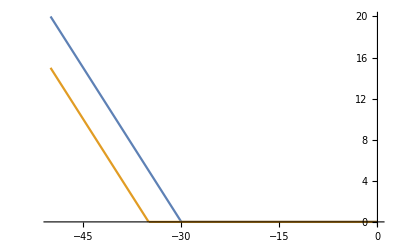

```mathematica
Plot[{
BypassIntFermi[x,-30+9.01+10,0,-150,-30,300],
BypassIntFermi[x,-30+9.01+10,5,-150,-30,300]},
{x,-50,0}]
```

With UnitStep distribution:

```mathematica
IntUstep=Integrate[ρU[x+δ,A,B]UnitStep[-x-δ],{x,ϵ,Γ},Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,δ>0,A<B,ϵ<B}]
```

UnitStep[-A+Γ+δ] UnitStep[Γ-ϵ] (-(UnitStep[-Γ-δ] UnitStep[A-Γ-δ] (-(-1+UnitStep[-A]) ((-B+Γ+δ+B UnitStep[B]) UnitStep[-Γ-δ] UnitStep[B-Γ-δ]+UnitStep[B] (B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ+δ])+UnitStep[-A] ((-A+Γ+δ) UnitStep[A-Γ-δ] UnitStep[B-Γ-δ]+(-A+B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[-A+Γ+δ]))+UnitStep[-A] UnitStep[-A+Γ+δ] ((A UnitStep[A] UnitStep[B]+UnitStep[-A] (A-B+B UnitStep[B])) (-1+UnitStep[-Γ-δ])+UnitStep[-Γ-δ] ((-A+Γ+δ) UnitStep[A-Γ-δ] UnitStep[B-Γ-δ]+(-A+B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[-A+Γ+δ]))) (-1+UnitStep[-A+δ+ϵ])+(UnitStep[-Γ-δ] UnitStep[-Γ+ϵ] (-((-B+Γ+δ+B UnitStep[B]) UnitStep[-Γ-δ] UnitStep[B-Γ-δ]+UnitStep[B] (B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ+δ]) (-1+UnitStep[-δ-ϵ])+UnitStep[-δ-ϵ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ]))+UnitStep[Γ-ϵ] UnitStep[-δ-ϵ] (UnitStep[-Γ-δ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ])-(-1+UnitStep[-Γ-δ]) (-(-B+δ+ϵ+B UnitStep[B]) UnitStep[-δ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B] (-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[δ+ϵ]))) UnitStep[-A+δ+ϵ])+UnitStep[-Γ+ϵ] UnitStep[-A+δ+ϵ] (UnitStep[-A+Γ+δ] (UnitStep[-Γ-δ] UnitStep[-Γ+ϵ] (-((-B+Γ+δ+B UnitStep[B]) UnitStep[-Γ-δ] UnitStep[B-Γ-δ]+UnitStep[B] (B+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ+δ]) (-1+UnitStep[-δ-ϵ])+UnitStep[-δ-ϵ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ]))+UnitStep[Γ-ϵ] UnitStep[-δ-ϵ] (UnitStep[-Γ-δ] ((B-δ-ϵ+(-B+Γ+δ) UnitStep[B-Γ-δ]) UnitStep[Γ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B-Γ-δ] (-B+Γ+δ+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-Γ+ϵ])-(-1+UnitStep[-Γ-δ]) (-(-B+δ+ϵ+B UnitStep[B]) UnitStep[-δ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B] (-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[δ+ϵ])))-(-1+UnitStep[-A+Γ+δ]) (UnitStep[-δ-ϵ] UnitStep[A-δ-ϵ] (-(-1+UnitStep[-A]) (-(-B+δ+ϵ+B UnitStep[B]) UnitStep[-δ-ϵ] UnitStep[B-δ-ϵ]+UnitStep[B] (-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[δ+ϵ])+UnitStep[-A] ((A-δ-ϵ) UnitStep[A-δ-ϵ] UnitStep[B-δ-ϵ]+(A-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-A+δ+ϵ]))+UnitStep[-A] UnitStep[-A+δ+ϵ] (-(A UnitStep[A] UnitStep[B]+UnitStep[-A] (A-B+B UnitStep[B])) (-1+UnitStep[-δ-ϵ])+UnitStep[-δ-ϵ] ((A-δ-ϵ) UnitStep[A-δ-ϵ] UnitStep[B-δ-ϵ]+(A-B+(B-δ-ϵ) UnitStep[B-δ-ϵ]) UnitStep[-A+δ+ϵ]))))

```mathematica
IntUsteps=FullSimplify[IntUstep,Assumptions->{A∈Reals,B∈Reals,Γ∈Reals,δ∈Reals,ϵ∈Reals,kT>0,δ>0,A<B,ϵ<B}]
```

Piecewise[{{0, (δ+ϵ≤0&&((Γ==ϵ&&B≥δ+ϵ&&A≤δ+ϵ)||(A≥δ+ϵ&&A>Γ+δ)||(B<Γ+δ&&((B<δ+ϵ&&Γ+δ≤0)||Γ<ϵ))))||(A≥0&&((A>Γ+δ&&δ+ϵ>0)||(A>δ+ϵ&&Γ+δ>0)))||(A>δ+ϵ&&((A>0&&A<Γ+δ)||(A≥Γ+δ&&Γ+δ≤0)||Γ<ϵ||A>Γ+δ))||(B<0&&((δ+ϵ>0&&B<Γ+δ)||(Γ+δ>0&&B<δ+ϵ)))||(B<Γ+δ&&Γ+δ<0&&(B<δ+ϵ||δ+ϵ>0))||(Γ<ϵ&&A≤Γ+δ&&((B≥Γ+δ&&Γ+δ≥0)||Γ+δ>0))||(B<δ+ϵ&&(δ+ϵ<0||Γ+δ≤0)&&(Γ>ϵ||Γ+δ>0))||(A>Γ+δ&&(A>0||Γ>ϵ))||(δ+ϵ>0&&A≤δ+ϵ&&((Γ+δ>0&&A≤Γ+δ)||Γ>ϵ))}, {-A, A<0&&B≥0&&Γ+δ>0&&A>δ+ϵ}, {A, A<0&&B≥0&&A>Γ+δ&&δ+ϵ>0}, {A-B, (B<0||δ+ϵ≤0)&&(B<δ+ϵ||δ+ϵ>0)&&A≤0&&A>Γ+δ&&Γ≤ϵ}, {-A+B, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&Γ≥ϵ&&A≤0&&A>δ+ϵ}, {Γ+δ, B≥0&&Γ+δ<0&&δ+ϵ>0&&A≤Γ+δ}, {-A+Γ+δ, A<Γ+δ&&B≥Γ+δ&&Γ+δ≤0&&A>δ+ϵ}, {-B+Γ+δ, (B<0||δ+ϵ≤0)&&B≥Γ+δ&&Γ<ϵ&&(B<δ+ϵ||δ+ϵ>0)&&A≤Γ+δ&&Γ+δ≤0}, {Γ-ϵ, B≥Γ+δ&&Γ≠ϵ&&B≥δ+ϵ&&A≤Γ+δ&&Γ+δ≤0&&A≤δ+ϵ&&δ+ϵ≤0}, {-δ-ϵ, B≥0&&δ+ϵ<0&&Γ+δ>0&&A≤δ+ϵ}, {A-δ-ϵ, A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ&&δ+ϵ≤0}, {B-δ-ϵ, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&B≥δ+ϵ&&Γ>ϵ&&A≤δ+ϵ&&δ+ϵ≤0}, {-2 (δ+ϵ), True}}]

```mathematica
TraditionalForm[IntUsteps]
```

Piecewise[{{0, (δ+ϵ≤0∧((Γ==ϵ∧B≥δ+ϵ∧A≤δ+ϵ)∨(A≥δ+ϵ∧A>Γ+δ)∨(B<Γ+δ∧((B<δ+ϵ∧Γ+δ≤0)∨Γ<ϵ))))∨(A≥0∧((A>Γ+δ∧δ+ϵ>0)∨(A>δ+ϵ∧Γ+δ>0)))∨(A>δ+ϵ∧((A>0∧A<Γ+δ)∨(A≥Γ+δ∧Γ+δ≤0)∨Γ<ϵ∨A>Γ+δ))∨(B<0∧((δ+ϵ>0∧B<Γ+δ)∨(Γ+δ>0∧B<δ+ϵ)))∨(B<Γ+δ∧Γ+δ<0∧(B<δ+ϵ∨δ+ϵ>0))∨(Γ<ϵ∧A≤Γ+δ∧((B≥Γ+δ∧Γ+δ≥0)∨Γ+δ>0))∨(B<δ+ϵ∧(δ+ϵ<0∨Γ+δ≤0)∧(Γ>ϵ∨Γ+δ>0))∨(A>Γ+δ∧(A>0∨Γ>ϵ))∨(δ+ϵ>0∧A≤δ+ϵ∧((Γ+δ>0∧A≤Γ+δ)∨Γ>ϵ))}, {-A, A<0∧B≥0∧Γ+δ>0∧A>δ+ϵ}, {A, A<0∧B≥0∧A>Γ+δ∧δ+ϵ>0}, {A-B, (B<0∨δ+ϵ≤0)∧(B<δ+ϵ∨δ+ϵ>0)∧A≤0∧A>Γ+δ∧Γ≤ϵ}, {B-A, (B<0∨Γ+δ≤0)∧(B<Γ+δ∨Γ+δ>0)∧Γ≥ϵ∧A≤0∧A>δ+ϵ}, {Γ+δ, B≥0∧Γ+δ<0∧δ+ϵ>0∧A≤Γ+δ}, {-A+Γ+δ, A<Γ+δ∧B≥Γ+δ∧Γ+δ≤0∧A>δ+ϵ}, {-B+Γ+δ, (B<0∨δ+ϵ≤0)∧B≥Γ+δ∧Γ<ϵ∧(B<δ+ϵ∨δ+ϵ>0)∧A≤Γ+δ∧Γ+δ≤0}, {Γ-ϵ, B≥Γ+δ∧Γ≠ϵ∧B≥δ+ϵ∧A≤Γ+δ∧Γ+δ≤0∧A≤δ+ϵ∧δ+ϵ≤0}, {-δ-ϵ, B≥0∧δ+ϵ<0∧Γ+δ>0∧A≤δ+ϵ}, {A-δ-ϵ, A<δ+ϵ∧B≥δ+ϵ∧A>Γ+δ∧δ+ϵ≤0}, {B-δ-ϵ, (B<0∨Γ+δ≤0)∧(B<Γ+δ∨Γ+δ>0)∧B≥δ+ϵ∧Γ>ϵ∧A≤δ+ϵ∧δ+ϵ≤0}, {-2 (δ+ϵ), True}}]

```mathematica
BypassIntStep[ϵ_,Γ_,δ_,A_,B_,T_]:=Module[{kT},
Piecewise[{{0, (δ+ϵ≤0&&((Γ==ϵ&&B≥δ+ϵ&&A≤δ+ϵ)||(A≥δ+ϵ&&A>Γ+δ)||(B<Γ+δ&&((B<δ+ϵ&&Γ+δ≤0)||Γ<ϵ))))||(A≥0&&((A>Γ+δ&&δ+ϵ>0)||(A>δ+ϵ&&Γ+δ>0)))||(A>δ+ϵ&&((A>0&&A<Γ+δ)||(A≥Γ+δ&&Γ+δ≤0)||Γ<ϵ||A>Γ+δ))||(B<0&&((δ+ϵ>0&&B<Γ+δ)||(Γ+δ>0&&B<δ+ϵ)))||(B<Γ+δ&&Γ+δ<0&&(B<δ+ϵ||δ+ϵ>0))||(Γ<ϵ&&A≤Γ+δ&&((B≥Γ+δ&&Γ+δ≥0)||Γ+δ>0))||(B<δ+ϵ&&(δ+ϵ<0||Γ+δ≤0)&&(Γ>ϵ||Γ+δ>0))||(A>Γ+δ&&(A>0||Γ>ϵ))||(δ+ϵ>0&&A≤δ+ϵ&&((Γ+δ>0&&A≤Γ+δ)||Γ>ϵ))}, {-A, A<0&&B≥0&&Γ+δ>0&&A>δ+ϵ}, {A, A<0&&B≥0&&A>Γ+δ&&δ+ϵ>0}, {A-B, (B<0||δ+ϵ≤0)&&(B<δ+ϵ||δ+ϵ>0)&&A≤0&&A>Γ+δ&&Γ≤ϵ}, {-A+B, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&Γ≥ϵ&&A≤0&&A>δ+ϵ}, {Γ+δ, B≥0&&Γ+δ<0&&δ+ϵ>0&&A≤Γ+δ}, {-A+Γ+δ, A<Γ+δ&&B≥Γ+δ&&Γ+δ≤0&&A>δ+ϵ}, {-B+Γ+δ, (B<0||δ+ϵ≤0)&&B≥Γ+δ&&Γ<ϵ&&(B<δ+ϵ||δ+ϵ>0)&&A≤Γ+δ&&Γ+δ≤0}, {Γ-ϵ, B≥Γ+δ&&Γ≠ϵ&&B≥δ+ϵ&&A≤Γ+δ&&Γ+δ≤0&&A≤δ+ϵ&&δ+ϵ≤0}, {-δ-ϵ, B≥0&&δ+ϵ<0&&Γ+δ>0&&A≤δ+ϵ}, {A-δ-ϵ, A<δ+ϵ&&B≥δ+ϵ&&A>Γ+δ&&δ+ϵ≤0}, {B-δ-ϵ, (B<0||Γ+δ≤0)&&(B<Γ+δ||Γ+δ>0)&&B≥δ+ϵ&&Γ>ϵ&&A≤δ+ϵ&&δ+ϵ≤0}, {-2 (δ+ϵ), True}}]];
```

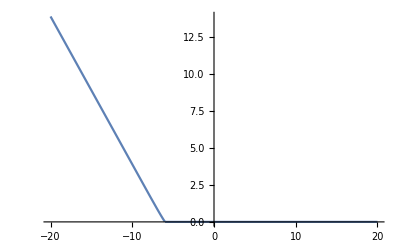

```mathematica
Plot[{BypassIntFermi[x,2,5,-100,-1,300],BypassIntStep[x,2,5,-100,-1]},{x,-20,20},PlotRange->All]
```

#### A function related to the adiabatic limit: ∑_α (|S_μα|)^2 f(Γ_μα)ρ_0(Γ_μα)

```mathematica
SSH[T_,Γ_,μ_,νmax_,R_,OptionsPattern[{Abottom->-150,Btop->-30}]]:=Module[{β,Γμα,Sμα,A,B,ss},
A=OptionValue[Abottom];
B=OptionValue[Btop];
β=1/(kb T au2kcal);
ss=0;
Do[
Γμα=Γ+(E2[α]-E2[0])au2kcal-(E1[μ]-E1[0])au2kcal;
Sμα=SHs[μ,α][R0[R]];
ss+=Sμα^2 1/(1+Exp[β Γμα])1/(B-A)UnitStep[Γμα-A]UnitStep[B-Γμα],
{α,0,νmax}];
ss
];
```

```mathematica
SSH[300.,-30.,0,5,3.2,Abottom->-150.,Btop->-30.]
```

3.39287×10^-7

```mathematica
Manipulate[
Plot[SSH[300,γ,μ,νmax,3.0,Abottom->-150,Btop->-30],{γ,-200,50},
Axes->False,Frame->True,
FrameLabel->{"Γ (kcal/mol)"," ∑"}],
{{μ,0,"Reactant state quantum number"},Range[0,10]},
{{νmax,10,"Highest product state quantum number"},Range[0,10]},
ControlType->Setter,FrameLabel->{None,None,"∑_α |S_μα|^2f(Γ+δϵ_α-δϵ_μ)ρ(Γ+δϵ_α-δϵ_μ)"},
LabelStyle->{FontSize->11}
]
```

```mathematica
NIntegrate[SSH[300,γ,0,10,3.0,Abottom->-150,Btop->-30],{γ,-200,0}]
```

0.998892

```mathematica
Δμ[T_,ϵ_,μ_,νmax_,R_,OptionsPattern[{Abottom->-150,Btop->-30}]]:=Module[{β,ϵα,Sμα,A,B,ss},
A=OptionValue[Abottom];
B=OptionValue[Btop];
β=1/(kb T au2kcal);
ss=0;
Do[
ϵα=ϵ+(E2[α]-E2[0])au2kcal;
Sμα=SHs[μ,α][R0[R]];
ss+=Sμα^2 1/(1+Exp[β ϵα])1/(B-A)UnitStep[ϵα-A]UnitStep[B-ϵα],
{α,0,νmax}];
ss
];
```

```mathematica
Manipulate[
Plot[Δμ[300,ϵ,μ,νmax,3.0,Abottom->-150,Btop->-30],{ϵ,-200,50},
Axes->False,Frame->True,
FrameLabel->{"ϵ (kcal/mol)","Δ_μ(ϵ)"}],
{{μ,0,"Reactant state quantum number"},Range[0,10]},
{{νmax,10,"Highest product state quantum number"},Range[0,10]},
ControlType->Setter,FrameLabel->{None,None,"∑_α |S_μα|^2f(ϵ+δϵ_α)ρ(ϵ+δϵ_α)"},
LabelStyle->{Blue,FontSize->11},Paneled->True
]
```

```mathematica
NIntegrate[Δμ[300,ϵ,0,10,3.0,Abottom->-150,Btop->-30],{ϵ,-200,0}]
```

0.998892

```mathematica
N@Integrate[HeavisideTheta[ϵ Sign[v]]Exp[-v^2-Abs[ϵ]/Abs[v]],{v,-∞,∞},{ϵ,-20,20}]
```

0.999996

```mathematica
Integrate[HeavisideTheta[ϵ Sign[v]]Exp[-v^2-Abs[ϵ]/Abs[v]],{v,-∞,∞},{ϵ,0,∞}]
```

1/2

#### PCET rate constant expression for a rectangular weighted density of states (flat band approximation)

```mathematica
kLZvib[T_,λ_,ΔG_,V0_,R_,μmax_,νmax_,
OptionsPattern[{
Distribution->"Fermi",
StatesPerAtom->1,
Abottom->-2ev2kcal,
Btop->2ev2kcal,
NAcorrection->False,
Isotope->"H",
PrintPartialRates->False}]
]:=Module[{ppr,isotope,ns,type,nac,dist,β,Z,Γ,f,W,M,Ξ,ΞS,ΞF,ΞSnac,ΞFnac,A,B,sum,ktot,kμ,ϵμ,ϵν,Γμ0,wμ,Δμ,bypassIntF,bypassIntS,nacIntF,nacIntS,Sμν,DOSrect},
ppr=OptionValue[PrintPartialRates];
isotope=OptionValue[Isotope];
nac=OptionValue[NAcorrection];
dist=OptionValue[Distribution];
ns=OptionValue[StatesPerAtom];
A=OptionValue[Abottom];
B=OptionValue[Btop];
Γ=ΔG+λ;
β=1/(kb T au2kcal);
DOSrect[ϵ_,A_,B_]:=UnitStep[ϵ-A]UnitStep[B-ϵ];
Z=Which[
isotope=="H",Sum[Exp[-β (E1[μ]-E1[0])au2kcal],{μ,0,μmax}],
isotope=="D",Sum[Exp[-β (E1D[μ]-E1D[0])au2kcal],{μ,0,μmax}]
];
f[ϵ_]:=Which[
dist=="Fermi",1/(1+Exp[β ϵ]),
dist=="Step",UnitStep[-ϵ]
];
M[v_]:=1/Ω √(β/(4π λ))Exp[-β v^2/(4 Ω^2 λ)];
Array[Sμν,{μmax+1,νmax+1},{0,0}];
Array[kμ,μmax+1,0];
Array[wμ,μmax+1,0];
Array[ϵν,νmax+1,0];
Do[
Which[
isotope=="H",Sμν[μ,ν]=SHs[μ,ν][R0[R]],
isotope=="D",Sμν[μ,ν]=SDs[μ,ν][R0[R]]
],
{μ,0,μmax},{ν,0,νmax}];
Do[
Which[
isotope=="H",ϵν[ν]=(E2[ν]-E2[0])au2kcal,
isotope=="D",ϵν[ν]=(E2D[ν]-E2D[0])au2kcal
],
{ν,0,νmax}];
(********************** Start summation over reactant states μ **********************)
ktot=0;
Do[
ϵμ=Which[
isotope=="H",(E1[μ]-E1[0])au2kcal,
isotope=="D",(E1D[μ]-E1D[0])au2kcal
];
wμ[μ]=Exp[-β ϵμ]/Z;
Γμ0=Γ-ϵμ;
Δμ[ϵ_]:=V0^2 ns/(B-A) Sum[(Sμν[μ,ν])^2×f[ϵ+ϵν[ν]]DOSrect[ϵ+ϵν[ν],A,B],{ν,0,νmax}];
bypassIntF[ϵ_]:=Sum[(Sμν[μ,ν])^2 Abs[BypassIntFermi[ϵ,Γμ0,ϵν[ν],A,B,T]],{ν,0,νmax}];
bypassIntS[ϵ_]:=Sum[(Sμν[μ,ν])^2 Abs[BypassIntStep[ϵ,Γμ0,ϵν[ν],A,B,T]],{ν,0,νmax}];
nacIntF[ϵ_]:=Sum[(Sμν[μ,ν])^2 Abs[2BypassIntFermi[ϵ,UnitStep[Γμ0-ϵ]A+UnitStep[ϵ-Γμ0]B,ϵν[ν],A,B,T]],{ν,0,νmax}];
nacIntS[ϵ_]:=Sum[(Sμν[μ,ν])^2 Abs[2BypassIntStep[ϵ,UnitStep[Γμ0-ϵ]A+UnitStep[ϵ-Γμ0]B,ϵν[ν],A,B]],{ν,0,νmax}];
ΞS[ϵ_,v_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[v])ns/(B-A)bypassIntS[ϵ]];
ΞF[ϵ_,v_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[v])ns/(B-A)bypassIntF[ϵ]];
ΞSnac[ϵ_,v_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[v])ns/(B-A)nacIntS[ϵ]];
ΞFnac[ϵ_,v_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[v])ns/(B-A)nacIntF[ϵ]];
W[ϵ_]:=√(β/(4π λ))Exp[-β(Γμ0-ϵ)^2/(4λ)];
Ξ[ϵ_,v_]:=Which[
dist=="Step",ΞS[ϵ,v]+If[nac,ΞSnac[ϵ,v],0],
dist=="Fermi",ΞF[ϵ,v]+If[nac,ΞFnac[ϵ,v],0],
True,0
];
kμ[μ]=(2π)/hbarkcalps
Quiet@NIntegrate[Δμ[ϵ]W[ϵ]
Quiet@NIntegrate[M[v]×UnitStep[Sign[v](ϵ-Γμ0)]×Ξ[ϵ,v],
{v,-∞,∞},WorkingPrecision->60,PrecisionGoal->20,Method->{Automatic,"SymbolicProcessing"->False}],
{ϵ,A-ϵν[νmax],B},WorkingPrecision->60,PrecisionGoal->20,Method->{Automatic,"SymbolicProcessing"->False}];
ktot+=wμ[μ]×kμ[μ],
{μ,0,μmax}];
If[ppr,
Print[
Grid[
Join[
{{"μ", "k_μ[ps^-1]","p_μk_μ[%]"}},
Table[{
μ,
ScientificForm[kμ[μ],6,ExponentFunction->(If[-3<#<3,Null,#]&)],
ScientificForm[(wμ[μ]kμ[μ])/ktot×100,6,ExponentFunction->(If[-3<#<3,Null,#]&)]
},{μ,0,μmax}],
{{"k_tot = "<>ToString[ktot]<>" ps^-1",SpanFromLeft}}
],
Frame->All,Background->{None,{1->Pink,-1->LightGreen}}
]
];
];
ktot
];
```

```mathematica
Options[NIntegrate]
```

{AccuracyGoal→∞,Compiled→Automatic,EvaluationMonitor→None,Exclusions→None,MaxPoints→Automatic,MaxRecursion→Automatic,Method→Automatic,MinRecursion→0,PrecisionGoal→Automatic,WorkingPrecision→MachinePrecision}

```mathematica
kLZvib[300,10,-9.5,1,2.3,2,3,Distribution->"Fermi",Isotope->"H",PrintPartialRates->True]
```

μ | k_μ[ps^-1] | p_μk_μ[%]
0 | 0.0238755 | 99.9999
1 | 0.489642 | 1.446×10^-4
2 | 0.7687 | 4.67183×10^-11
k_tot = 0.0238756 ps^-1 |  |

```mathematica
{kLZvib[300,10,-32,40,2.2,0,3,Distribution->"Fermi",Isotope->"H"],Ω/π}
```

{4.5977917669307355664899316627562972142247050182811,4.61549334966496473729762913780291649899932972647324}

### Reaction free energies for Volmer reaction (from Yan-Choi)

```mathematica
DGneg1120mV00HTab1aA={{0.2,7.426415919170871},{0.22,7.7487726567555395},{0.24000000000000002,8.010277248063828},{0.26,8.216724630030578},{0.28,8.373505192427087},{0.30000000000000004,8.485620689998745},{0.32,8.557700319846967},{0.34,8.59401703840082},{0.36,8.598504153512708},{0.38,8.574772188686945},{0.4,8.526125980600986},{0.42000000000000004,8.455581939965478},{0.44,8.365885381004636},{0.46,8.259527807412326},{0.48000000000000004,8.13876403288182},{0.5,8.005629011956263},{0.52,7.861954261196843},{0.54,7.709383760389763},{0.56,7.549389237331891},{0.5800000000000001,7.383284756264285},{0.6000000000000001,7.212240547922404},{0.62,7.0372960372820526},{0.64,6.859372042466415},{0.66,6.679282134240207},{0.6799999999999999,6.497743159597761},{0.7,6.315384944895506},{0.72,6.132759203716727},{0.74,5.950347682241354},{0.76,5.768569580479728},{0.78,5.58778829152763},{0.8,5.408317503253823}};
```

```mathematica
DGneg1120mV=Interpolation[DGneg1120mV00HTab1aA,Method->"Spline",InterpolationOrder->3];
```

### Plots of rate constants for (filled) d-band:

The d-band of bulk gold goes from (approximately) -150 kcal/mol to -30 kcal/mol (Fermi level is zero)
The d_(z^2)-band of gold surface should be much narrower.

Alkaline Conditions at -1.12 V vs. SHE, for an electron at the top of the d-band
V_d = 50 kcal/mol at R_(Au-O) = 3.0 Å -- decreases exponentially with β = 1.0 Å^-1, ω_X = 14.5 ps^-1, λ = 10 kcal/mol,
D_(Au-H) = 52 kcal/mol, D_(O-H) = 119 kcal/mol,  ω_(Au-H) = 1880 cm^-1, ω_(O-H) = 3450 cm^-1, r^eq(Au-H) = 1.6 Å, r^eq(O-H) = 0.976 Å, 
ϵ_top = -30 kcal/mol, ϵ_bottom = -150 kcal/mol

```mathematica
dBottom=-150;
dTop=-30;
Vd0=50;
Rd0=3;
βVd=1;
Vd[R_]:=Vd0 Exp[-βVd(R-Rd0)];
```

Calculation on the grid of V_0 values:

```mathematica
tStart=TimeUsed[];
dd=0.3;
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0A=dTop-8; (* Intrinsic bias in kcal/mol (with zero point energies included) *)
R=RDA[dd a2bohr];
μmax=1;
νmax=5;
NAC=False;
LZgridA=Union[Table[x,{x,0.1,1.0,0.2}],Table[x,{x,1,10,1.0}],Table[x,{x,10,100,10.0}],Table[x,{x,100,500,100.0}]];
LDKgridA=Union[Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,10.0,1}],Table[x,{x,10,100,10.0}]];
t0=TimeUsed[];
Monitor[
LZFermiListA=Table[{Δ,kLZvib[T,λ,ΔG0A,Δ,R,μmax,νmax,Distribution->"Fermi",Abottom->dBottom,Btop->dTop,NAcorrection->NAC]},{Δ,LZgridA}],
Row[{"(1) LZ with Fermi distribution: V_0 = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgridA,Δ]⟦1,1⟧,{1,Length[LZgridA]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
t1=TimeUsed[];
Panel[Style["LZ(Fermi) time/eval: "<>ToString[(t1-t0)/Length[LZgridA]]<>" seconds",Blue,12]]
t0=TimeUsed[];
Monitor[
LDKFermiListA=Table[{Δ,kLDKvib[T,λ,ΔG0A,Δ,R,μmax,νmax,Distribution->"Fermi",Abottom->dBottom,Btop->dTop]},{Δ,LDKgridA}],
Row[{"(2) FGR with Unit Step distribution: V_0 = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgridA,Δ]⟦1,1⟧,{1,Length[LDKgridA]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
SClimitA=If[ΔG0A+λ>0,kSCvibZusman[T,λ,ΔG0A,τL,μmax,Isotope->"H"],2/τL];
LZSCListA=Table[{LZgrid⟦i⟧,(LZFermiListA⟦i,2⟧SClimitA)/(LZFermiListA⟦i,2⟧+SClimitA)},{i,1,Length[LZgridA]}];
t1=TimeUsed[];
Panel[Style["LDK(Fermi) time/eval: "<>ToString[(t1-t0)/Length[LDKgridA]]<>" seconds",Blue,12]]
Speak["Calculation for normal region is finished. Thank you."];
EmitSound[Sound[{
SoundNote["E2",0.5,"ElectricBass"],
SoundNote["D2",0.25,"ElectricBass"],
SoundNote["E2",0.5,"ElectricBass"],
SoundNote["G2",0.5,"ElectricBass"],
SoundNote["E2",0.5,"ElectricBass"],
SoundNote["D2",0.25,"ElectricBass"],
SoundNote["E2",0.25,"ElectricBass"]
}]];
tEnd=TimeUsed[];
Panel[Style["Total time elapsed: "<>ToString[tEnd-tStart]<>" seconds",Red,12],FrameMargins->10]
```

LZ(Fermi) time/eval: 48.4428 seconds

Part::partd: Part specification LZgrid⟦1⟧ is longer than depth of object.

Part::partd: Part specification LZgrid⟦2⟧ is longer than depth of object.

Part::partd: Part specification LZgrid⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

LDK(Fermi) time/eval: 0.0466393 seconds

Total time elapsed: 1357.97 seconds

💡\[MathematicaIcon]☺ Let’s plot it!

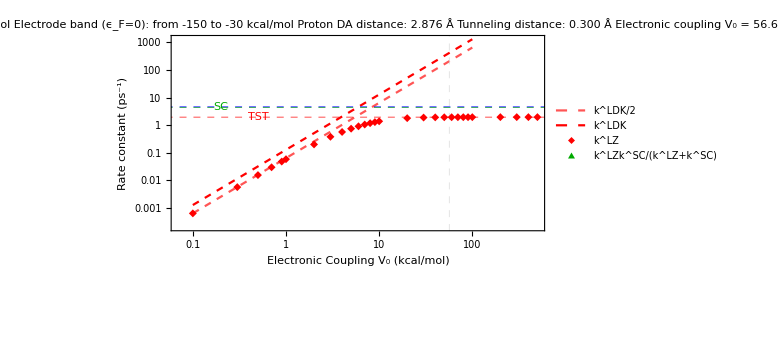

```mathematica
V0=Vd[RDA[dd a2bohr]];
ListLogLogPlot[{
Tooltip[MapAt[#/2&,LDKFermiListA,{All,2}],"FGR/2",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LDKFermiListA,"FGR",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LZFermiListA,"LZ(Fermi)",TooltipStyle->Directive[Blue,Bold,FontSize->18]],
Tooltip[LZSCListA,"LZ-SC(Fermi)",TooltipStyle->Directive[Darker[Green],Bold,FontSize->18]]
},
GridLines->{{V0},{{SClimitA,Darker[Green]},{Ω/(2π)PΓ[T,λ,ΔG0A,Min[0,dTop]],Red},{Ω/π,Blue}}},
GridLinesStyle->Directive[Dashed,Thin],
PlotLabel->Column[{
If[ΔG0A+λ<0,
Style["Inverted Region: ΔG + λ = "<>ToString[NumberForm[ΔG0A+λ,{4,3}]]<>" kcal/mol",Black,12],
Style["Normal Region: ΔG + λ = "<>ToString[NumberForm[ΔG0A+λ,{4,3}]]<>" kcal/mol",Black,12]],
Style["Electrode band (ϵ_F=0): from "<>ToString[NumberForm[dBottom,{4,3}]]<>" to "<>ToString[NumberForm[dTop,{4,3}],StandardForm]<> " kcal/mol",Black,12],
Style["Proton DA distance: "<>ToString[NumberForm[R,{4,3}]]<>" Å",Black,12],
Style["Tunneling distance: "<>ToString[NumberForm[dd,{4,3}]]<>" Å",Black,12],
Style["Electronic coupling V_0 = "<>ToString[V0]<>" kcal/mol",Black,12],
Style["Proton vibrational overlap <0|0>: "<>ToString[ScientificForm[SHs[0,0][R0[R]],6,NumberFormat->(Row[{#1,"E",#3}]&)]],Black,12],
Style["Reactant and product proton states: (0..."<>ToString[μmax]<>")→(0..."<>ToString[νmax]<>")",Black,12],
Style["Recrossing corrections: "<>ToString[NAC],Black,12]
},Spacings->0,Frame->None],
ImageSize->Large,Joined->{True,True,False,False},
PlotStyle->{{Lighter[Red],Dashed},{Red,Dashed},Red,Darker[Green]},
PlotMarkers->{None,None,Automatic,Automatic},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"k^LDK/2",
"k^LDK",
"k^LZ",
"k^LZk^SC/(k^LZ+k^SC)"
},LegendFunction->None,LabelStyle->12,LegendLayout->"Column"],{0.5,0.2}],
Epilog->{
Text[Style["SC",Darker[Green],Background->White],{Log[0.2],Log[SClimitA]}],
Text[Style["TST",Red,Background->White],{Log[0.5],Log[Ω/(2π)PΓ[T,λ,ΔG0A,Min[0,dTop]]]}],
Text[Style["Ω/π",Blue,Background->White],{Log[0.02],Log[Ω/π]}],
Text[Style["V_0",Black,Background->White],{Log[V0],Log[10^-9]}]
},
FrameLabel->{"Electronic Coupling V_0 (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

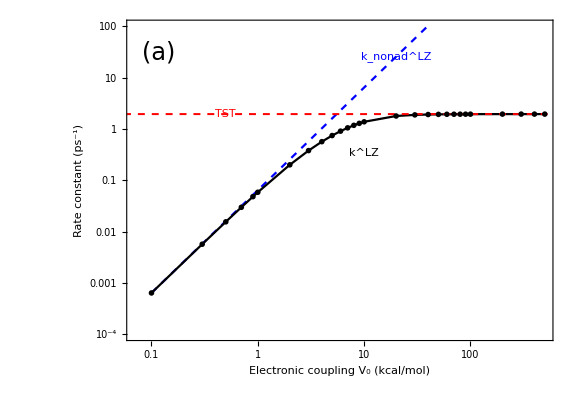

```mathematica
V0=Vd[RDA[dd a2bohr]];
imgSize=Large;
imgPadding={{100,20},{60,20}};
fig3a=ListLogLogPlot[{
Tooltip[MapAt[#/2&,LDKFermiListA,{All,2}],"FGR/2",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LZFermiListA,"LZ(Fermi)",TooltipStyle->Directive[Blue,Bold,FontSize->18]]
},
GridLines->{None,{{Ω/(2π)PΓ[T,λ,ΔG0A,Min[0,dTop]],Red}}},
GridLinesStyle->Directive[Dashed,Thickness[0.0025]],
ImageSize->imgSize,
ImagePadding->imgPadding,
Joined->{True,True,True},
PlotStyle->{{Blue,Dashed},Black},
PlotMarkers->{None,"OpenMarkers"},
PlotRange->{10^-4,10^2},
Axes->False,Frame->True,
Epilog->{
Text[Style["TST",Red,Background->White],{Log[0.5],Log[Ω/(2π)PΓ[T,λ,ΔG0A,Min[0,dTop]]]}],
Text[Style["k_nonad^LZ",Blue,Background->White],{Log[20],Log[LDKFermiListA⟦22,2⟧/2]}],
Text[Style["k^LZ",Black,Background->White],{Log[10],Log[LZFermiListA⟦15,2⟧/4]}],
Text[Style["(a)",Black,FontSize->24,Background->White],Scaled[{0.075,0.9}]]
},
FrameLabel->{"Electronic coupling V_0 (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24,Black},
FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->0.7]
```

```mathematica
Export["fig3a.eps",fig3a,ImageResolution->300,ImageSize->900];
Export["fig3a.pdf",fig3a,ImageResolution->300,ImageSize->900];
Export["fig3a.tiff",fig3a,ImageResolution->300,ImageSize->900];
Export["fig3a.png",fig3a,ImageResolution->300,ImageSize->900];
```

### Plots of rate constants for (extended) sp-band:

The sp-band of bulk gold goes from (approximately) -200 kcal/mol to 200 kcal/mol (Fermi level is zero)

Alkaline Conditions at -1.12 V vs. SHE, for an electron at the Fermi level
V_sp = 50 kcal/mol at R_(Au-O) = 3.0 Å -- decreases exponentially with β = 1.0 Å^-1, ω_X = 14.5 ps^-1, λ = 10 kcal/mol,
D_(Au-H) = 52 kcal/mol, D_(O-H) = 119 kcal/mol,  ω_(Au-H) = 1880 cm^-1, ω_(O-H) = 3450 cm^-1, r^eq(Au-H) = 1.6 Å, r^eq(O-H) = 0.976 Å, 
ϵ_top = 200 kcal/mol, ϵ_bottom = -200 kcal/mol

```mathematica
spBottom=-200;
spTop=200;
Vsp0=50;
Rsp0=3;
βVsp=1;
Vsp[R_]:=Vsp0 Exp[-βVsp(R-Rsp0)];
```

Calculation on the grid of V_0 values:

```mathematica
tStart=TimeUsed[];
dd=0.3;
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0B=-8; (* Intrinsic bias in kcal/mol (with zero point energies included) *)
R=RDA[dd a2bohr];
μmax=1;
νmax=5;
NAC=False;
LZgridB=Union[Table[x,{x,0.1,1.0,0.2}],Table[x,{x,1,10,1.0}],Table[x,{x,10,100,10.0}],Table[x,{x,100,500,100.0}]];
LDKgridB=Union[Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,10.0,1}],Table[x,{x,10,100,10.0}]];
t0=TimeUsed[];
Monitor[
LZFermiListB=Table[{Δ,kLZvib[T,λ,ΔG0B,Δ,R,μmax,νmax,Distribution->"Fermi",Abottom->spBottom,Btop->spTop,NAcorrection->NAC]},{Δ,LZgridB}],
Row[{"(1) LZ with Fermi distribution: V_0 = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgridB,Δ]⟦1,1⟧,{1,Length[LZgridB]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
t1=TimeUsed[];
Panel[Style["LZ(Fermi) time/eval: "<>ToString[(t1-t0)/Length[LZgridB]]<>" seconds",Blue,12]]
t0=TimeUsed[];
Monitor[
LDKFermiListB=Table[{Δ,kLDKvib[T,λ,ΔG0B,Δ,R,μmax,νmax,Distribution->"Fermi",Abottom->spBottom,Btop->spTop]},{Δ,LDKgridB}],
Row[{"(2) FGR with Unit Step distribution: V_0 = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgridB,Δ]⟦1,1⟧,{1,Length[LDKgridB]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
SClimitB=If[ΔG0B+λ>0,kSCvibZusman[T,λ,ΔG0B,τL,μmax,Isotope->"H"],2/τL];
LZSCListB=Table[{LZgridB⟦i⟧,(LZFermiListB⟦i,2⟧SClimitB)/(LZFermiListB⟦i,2⟧+SClimitB)},{i,1,Length[LZgridB]}];
t1=TimeUsed[];
Panel[Style["LDK(Fermi) time/eval: "<>ToString[(t1-t0)/Length[LDKgridB]]<>" seconds",Blue,12]]
Speak["Calculation for normal region is finished. Thank you."];
EmitSound[Sound[{
SoundNote["E2",0.5,"ElectricBass"],
SoundNote["D2",0.25,"ElectricBass"],
SoundNote["E2",0.5,"ElectricBass"],
SoundNote["G2",0.5,"ElectricBass"],
SoundNote["E2",0.5,"ElectricBass"],
SoundNote["D2",0.25,"ElectricBass"],
SoundNote["E2",0.25,"ElectricBass"]
}]];
tEnd=TimeUsed[];
Panel[Style["Total time elapsed: "<>ToString[tEnd-tStart]<>" seconds",Red,12],FrameMargins->10]
```

LZ(Fermi) time/eval: 38.2656 seconds

LDK(Fermi) time/eval: 0.0422651 seconds

Total time elapsed: 1072.74 seconds

💡\[MathematicaIcon]☺ Let’s plot it!

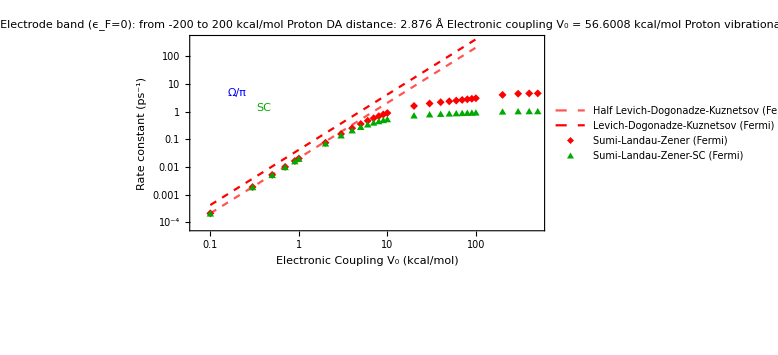

```mathematica
V0=Vsp[RDA[dd a2bohr]];
ListLogLogPlot[{
Tooltip[MapAt[#/2&,LDKFermiListB,{All,2}],"FGR/2",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LDKFermiListB,"FGR",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LZFermiListB,"LZ(Fermi)",TooltipStyle->Directive[Blue,Bold,FontSize->18]],
Tooltip[LZSCListB,"LZ-SC(Fermi)",TooltipStyle->Directive[Darker[Green],Bold,FontSize->18]]
},
GridLines->{{50},{{SClimitB,Darker[Green]},{Ω/(2π)PΓ[T,λ,ΔG0B,Min[0,dTop]],Red},{Ω/π,Blue}}},
GridLinesStyle->Directive[Dashed,Thin],
PlotLabel->Column[{
If[ΔG0B+λ<0,
Style["Inverted Region: ΔG + λ = "<>ToString[NumberForm[ΔG0B+λ,{4,3}]]<>" kcal/mol",Black,12],
Style["Normal Region: ΔG + λ = "<>ToString[NumberForm[ΔG0B+λ,{4,3}]]<>" kcal/mol",Black,12]],
Style["Electrode band (ϵ_F=0): from "<>ToString[NumberForm[spBottom,{4,3}]]<>" to "<>ToString[NumberForm[spTop,{4,3}],StandardForm]<> " kcal/mol",Black,12],
Style["Proton DA distance: "<>ToString[NumberForm[R,{4,3}]]<>" Å",Black,12],
Style["Electronic coupling V_0 = "<>ToString[V0]<>" kcal/mol",Black,12],
Style["Proton vibrational overlap <0|0>: "<>ToString[ScientificForm[SHs[0,0][R0[R]],6,NumberFormat->(Row[{#1,"E",#3}]&)]],Black,12],
Style["Reactant and product proton states: (0..."<>ToString[μmax]<>")→(0..."<>ToString[νmax]<>")",Black,12],
Style["Recrossing corrections: "<>ToString[NAC],Black,12]
},Spacings->0,Frame->None],
ImageSize->Large,Joined->{True,True,False,False},
PlotStyle->{{Lighter[Red],Dashed},{Red,Dashed},Red,Darker[Green]},
PlotMarkers->{None,None,Automatic,Automatic},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"Half Levich-Dogonadze-Kuznetsov (Fermi)",
"Levich-Dogonadze-Kuznetsov (Fermi)",
"Sumi-Landau-Zener (Fermi)",
"Sumi-Landau-Zener-SC (Fermi)"
},LegendFunction->"Frame",LabelStyle->12,LegendLayout->"Column"],{0.65,0.2}],
Epilog->{
Text[Style["SC",Darker[Green],Background->White],{Log[0.4],Log[SClimitB]}],
Text[Style["TST",Red,Background->White],{Log[0.005],Log[Ω/(2π)PΓ[T,λ,ΔG0B,Min[0,dTop]]]}],
Text[Style["Ω/π",Blue,Background->White],{Log[0.2],Log[Ω/π]}],
Text[Rotate[Style["V_0",Black,Background->White],0],{Log[V0],Log[10^-8]}]
},
FrameLabel->{"Electronic Coupling V_0 (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

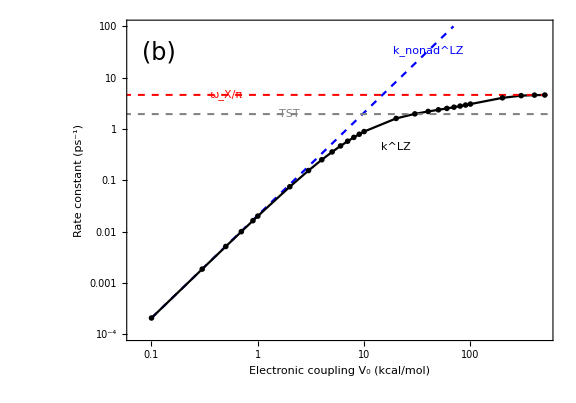

```mathematica
imgSize=Large;
imgPadding={{100,20},{60,20}};
fig3b=ListLogLogPlot[{
Tooltip[MapAt[#/2&,LDKFermiListB,{All,2}],"FGR/2",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LZFermiListB,"LZ(Fermi)",TooltipStyle->Directive[Blue,Bold,FontSize->18]]
},
GridLines->{None,{{Ω/π,Red},{Ω/(2π)PΓ[T,λ,ΔG0B,Min[0,spTop]],Gray}}},
GridLinesStyle->Directive[Dashed,Thickness[0.0025]],
ImageSize->imgSize,
ImagePadding->imgPadding,
Joined->{True,True},
PlotStyle->{{Blue,Dashed},Black},
PlotMarkers->{None,"OpenMarkers"},
PlotRange->{10^-4,10^2},
Axes->False,Frame->True,
Epilog->{
Text[Style["k_nonad^LZ",Blue,Background->White],{Log[40],Log[LDKFermiListB⟦24,2⟧/2]}],
Text[Style["k^LZ",Black,Background->White],{Log[20],Log[LZFermiListB⟦15,2⟧/2]}],
Text[Style["(b)",Black,Background->White,FontSize->24],Scaled[{0.075,0.9}]],
Text[Style["ω_X/π",Red,Background->White],{Log[0.5],Log[Ω/π]}],
Text[Style["TST",Gray,Background->White],{Log[2],Log[Ω/(2π)PΓ[T,λ,ΔG0B,Min[0,spTop]]]}]
},
FrameLabel->{"Electronic coupling V_0 (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->24,Black},
FrameStyle->Directive[Black,Thickness[0.003]],AspectRatio->0.7]
```

```mathematica
Export["fig3b.eps",fig3b,ImageResolution->300,ImageSize->900];
Export["fig3b.pdf",fig3b,ImageResolution->300,ImageSize->900];
Export["fig3b.tiff",fig3b,ImageResolution->300,ImageSize->900];
Export["fig3b.png",fig3b,ImageResolution->300,ImageSize->900];
```

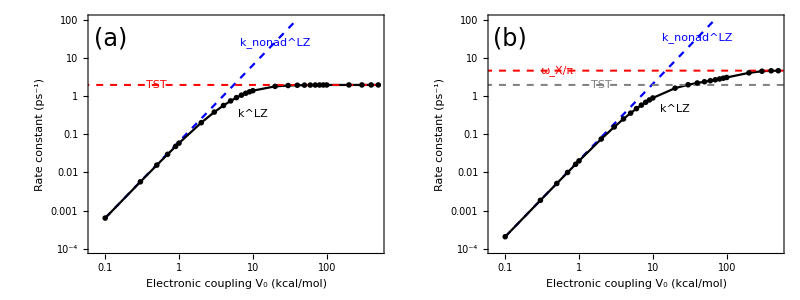

```mathematica
fig3=Grid[{{fig3a,fig3b}}]
```

```mathematica
Export["fig3.eps",fig3,ImageResolution->300];
Export["fig3.pdf",fig3,ImageResolution->300];
Export["fig3.tiff",fig3,ImageResolution->300];
Export["fig3.png",fig3,ImageResolution->300];
```

### General (including inverted region)

```mathematica
tStart=TimeUsed[];
T=300; (* Temperature in K *)
λ=10; (* reorganization energy in kcal/mol *)
ΔG0I=-15; (* Intrinsic bias in kcal/mol *)
dBottom=-40;
dTop=40;
R=RAH+RDH;
μmax=0;
νmax=0;
NAC=False;
LZgrid=Union[Table[x,{x,0.001,0.01,0.002}],Table[x,{x,0.01,0.1,0.02}],Table[x,{x,0.1,1.0,0.2}],Table[x,{x,1,10,1.0}],Table[x,{x,10,50,5}]];
LDKgrid=Union[Table[x,{x,0.001,0.01,0.001}],Table[x,{x,0.01,0.1,0.01}],Table[x,{x,0.1,1.0,0.1}],Table[x,{x,1,5.0,1}]];
t0=TimeUsed[];
Monitor[
LZFermiListI=Table[{Δ,kLZvib[T,λ,ΔG0I,Δ,R,μmax,νmax,Distribution->"Fermi",Abottom->dBottom,Btop->dTop,NAcorrection->NAC]},{Δ,LZgrid}],
Row[{"(1) LZ with Fermi distribution: V_0 = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LZgrid,Δ]⟦1,1⟧,{1,Length[LZgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
t1=TimeUsed[];
Panel[Style["LZ(Fermi) time/eval: "<>ToString[(t1-t0)/Length[LZgrid]]<>" seconds",Blue,12]]
t0=TimeUsed[];
Monitor[
LDKFermiListI=Table[{Δ,kLDKvib[T,λ,ΔG0I,Δ,R,μmax,νmax,Distribution->"Fermi",Abottom->dBottom,Btop->dTop]},{Δ,LDKgrid}],
Row[{"(2) FGR with Unit Step distribution: V_0 = ",NumberForm[Δ,{5,4}]," kcal/mol ",ProgressIndicator[Position[LDKgrid,Δ]⟦1,1⟧,{1,Length[LDKgrid]}]},Frame->True,Background->Yellow,RoundingRadius->5]
];
SClimitI=If[ΔG0I+λ>0,kSCvibZusman[T,λ,ΔG0I,τL,μmax,Isotope->"H"],1/τL];
LZSCListI=Table[{LZgrid⟦i⟧,(LZFermiListI⟦i,2⟧SClimitI)/(LZFermiListI⟦i,2⟧+SClimitI)},{i,1,Length[LZgrid]}];
t1=TimeUsed[];
Panel[Style["LDK(Fermi) time/eval: "<>ToString[(t1-t0)/Length[LDKgrid]]<>" seconds",Blue,12]]
Speak["Calculation for inverted region is finished. Thank you."];
EmitSound[Sound[{
SoundNote["E2",0.5,"RockOrgan"],
SoundNote["D2",0.25,"RockOrgan"],
SoundNote["E2",0.5,"RockOrgan"],
SoundNote["G2",0.5,"RockOrgan"],
SoundNote["E2",0.5,"RockOrgan"],
SoundNote["D2",0.25,"RockOrgan"],
SoundNote["E2",0.25,"RockOrgan"]
}]];
tEnd=TimeUsed[];
Panel[Style["Total time elapsed: "<>ToString[tEnd-tStart]<>" seconds",Red,12],FrameMargins->10]
```

LZ(Fermi) time/eval: 11.1633 seconds

LDK(Fermi) time/eval: 0.0037576 seconds

Total time elapsed: 379.711 seconds

Let’s plot it!

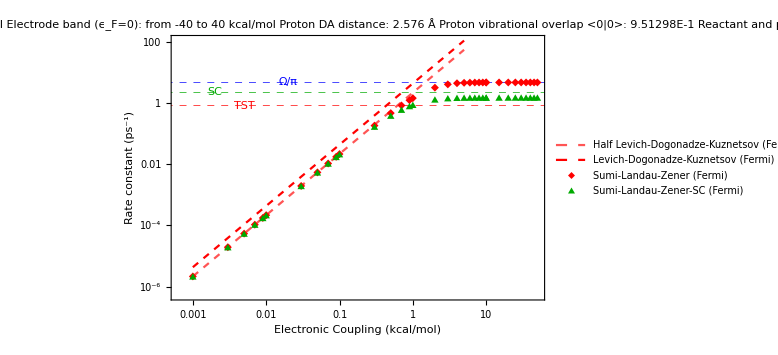

```mathematica
ListLogLogPlot[{
Tooltip[MapAt[#/2&,LDKFermiListI,{All,2}],"FGR/2",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LDKFermiListI,"FGR",TooltipStyle->Directive[Black,Bold,FontSize->18]],
Tooltip[LZFermiListI,"LZ(Fermi)",TooltipStyle->Directive[Blue,Bold,FontSize->18]],
Tooltip[LZSCListI,"LZ-SC(Fermi)",TooltipStyle->Directive[Darker[Green],Bold,FontSize->18]]
},
GridLines->{None,{{SClimitI,Darker[Green]},{Ω/(2π)PΓ[T,λ,ΔG0I,Min[0,dTop]],Red},{Ω/π,Blue}}},
GridLinesStyle->Directive[Dashed,Thin],
PlotLabel->Column[{
If[ΔG0I+λ<0,
Style["Inverted Region: ΔG + λ = "<>ToString[NumberForm[ΔG0I+λ,{4,3}]]<>" kcal/mol",Black,12],
Style["Normal Region: ΔG + λ = "<>ToString[NumberForm[ΔG0I+λ,{4,3}]]<>" kcal/mol",Black,12]],
Style["Electrode band (ϵ_F=0): from "<>ToString[NumberForm[dBottom,{4,3}]]<>" to "<>ToString[NumberForm[dTop,{4,3}],StandardForm]<> " kcal/mol",Black,12],
Style["Proton DA distance: "<>ToString[NumberForm[R,{4,3}]]<>" Å",Black,12],
Style["Proton vibrational overlap <0|0>: "<>ToString[ScientificForm[SHs[0,0][R0[R]],6,NumberFormat->(Row[{#1,"E",#3}]&)]],Black,12],
Style["Reactant and product proton states: (0..."<>ToString[μmax]<>")→(0..."<>ToString[νmax]<>")",Black,12],
Style["Recrossing corrections: "<>ToString[NAC],Black,12]
},Spacings->0,Frame->None],
ImageSize->Large,Joined->{True,True,False,False},
PlotStyle->{{Lighter[Red],Dashed},{Red,Dashed},Red,Darker[Green]},
PlotMarkers->{None,None,Automatic,Automatic},
PlotRange->All,
Axes->False,Frame->True,
PlotLegends->Placed[LineLegend[{
"Half Levich-Dogonadze-Kuznetsov (Fermi)",
"Levich-Dogonadze-Kuznetsov (Fermi)",
"Sumi-Landau-Zener (Fermi)",
"Sumi-Landau-Zener-SC (Fermi)"
},LegendFunction->"Frame",LabelStyle->12,LegendLayout->"Column"],{0.65,0.2}],
Epilog->{
Text[Style["SC",Darker[Green],Background->White],{Log[0.002],Log[SClimitI]}],
Text[Style["TST",Red,Background->White],{Log[0.005],Log[Ω/(2π)PΓ[T,λ,ΔG0I,Min[0,dTop]]]}],
Text[Style["Ω/π",Blue,Background->White],{Log[0.02],Log[Ω/π]}]
},
FrameLabel->{"Electronic Coupling (kcal/mol)","Rate constant (ps^-1)"},
BaseStyle->{FontFamily->"Helvetica",FontSize->16,Black},
FrameStyle->Black]
```

```mathematica
LZFermiList
```

$Aborted

### Trying to understand the adiabatic limit

```mathematica
Normal@Series[Exp[(Γ+x)/kT],{x,0,1}]
```

ⅇ^(Γ/kT)+(ⅇ^(Γ/kT) x)/kT

```mathematica
Normal@Series[Γ-ϵ+kT Log[(1+Exp[ϵ/kT])/(1+Exp[Γ/kT])],{ϵ,Γ,1},Assumptions->{kT>0,Γ∈Reals,ϵν>0}]//FullSimplify
```

(Γ-ϵ)/(1+ⅇ^(Γ/kT))

```mathematica
FullSimplify[%,Assumptions->{kT>0,Γ∈Reals}]
```

(Γ-ϵ)/(1+ⅇ^(Γ/kT))

```mathematica
Series[V^2 1/(1+Exp[ϵ])Exp[-V^2/v(Γ+Log[(1+ⅇ^(-ϵ/kT))/(1+ⅇ^(Γ/kT))])],{V,∞,2},Assumptions->{v>0,ϵ∈Reals,kT>0,Γ>0}]
```

ⅇ^(-((Γ+Log[(1+ⅇ^(-ϵ/kT))/(1+ⅇ^(Γ/kT))]) V^2)/v+O[1/V]^3) (V^2/(1+ⅇ^ϵ)+O[1/V]^3)

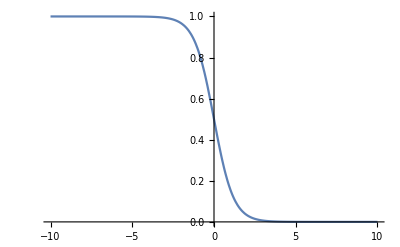

```mathematica
Plot[1/(1+Exp[ϵ/(kb 300 au2kcal)]),{ϵ,-10,10}]
```

```mathematica
Integrate[V^2 Exp[-v^2]Exp[-(ϵ V^2)/Abs[v]],{v,-∞,∞},Assumptions->{V>0,ϵ>0}]
```

(V^4 ϵ MeijerG[{{},{}},{{-1/2,0,0},{}},(V^4 ϵ^2)/4])/(2 √π)

```mathematica
f[V_,ϵ_]:=(V^4 ϵ MeijerG[{{},{}},{{-1/2,0,0},{}},(ϵ^2 V^4)/4])/(2 √π);
```

```mathematica
Series[f[V,ϵ],{V,∞,2},{ϵ,0,2},Assumptions->{ϵ>0}]
```

ⅇ^((-(3 ϵ^(2/3))/2^(2/3)+O[ϵ]^(8/3)) V^(4/3)+O[1/V]^(19/3)) (4 √(π/3) V^2+(-(2^(2/3) √(π/3))/(9 ϵ^(2/3))+O[ϵ]^(7/3)) V^(2/3)+((25 √(π/3))/(162 2^(2/3) ϵ^(4/3))+O[ϵ]^(7/3)) (1/V)^(2/3)+O[1/V]^(7/3))

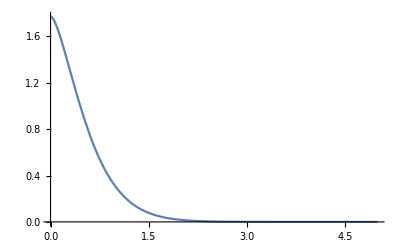

```mathematica
Plot[f[V],{V,0,5},PlotRange->All]
```

```mathematica
Limit[f[V],V->0,Direction->-1]
```

√π

```mathematica
f[0]
```

Power::infy: Infinite expression 1/0. encountered.

0.282095 MeijerG[{{},{}},{{-0.5,0.,0.},{}},0.]

```mathematica
Series[Exp[-1/v Δ ϵ],{ϵ,0,2},Assumptions->{v>0,Δ>0}]
```

1-(Δ ϵ)/v+(Δ^2 ϵ^2)/(2 v^2)+O[ϵ]^3

```mathematica
LZad[T_,λ_,ΔG_,V0_,ϵ_,v_,
OptionsPattern[{
Distribution->"Fermi",
StatesPerAtom->1,
Abottom->-2ev2kcal,
Btop->2ev2kcal,
NAcorrection->False}]]:=
Module[{ns,type,nac,dist,β,Γ,f,W,M,Ξ,ΞS,ΞF,ΞSnac,ΞFnac,A,B,sum,ktot,kμ,ϵμ,ϵν,Γμ0,wμ,Δ,bypassIntF,bypassIntS,nacIntF,nacIntS,Sμν,DOSrect},
nac=OptionValue[NAcorrection];
dist=OptionValue[Distribution];
ns=OptionValue[StatesPerAtom];
A=OptionValue[Abottom];
B=OptionValue[Btop];
Γ=ΔG+λ;
β=1/(kb T au2kcal);
DOSrect[x_,A_,B_]:=UnitStep[x-A]UnitStep[B-x];
f[x_]:=Which[
dist=="Fermi",1/(1+Exp[β x]),
dist=="Step",UnitStep[-x]
];
M[x_]:=1/Ω √(β/(4π λ))Exp[-β x^2/(4 Ω^2 λ)];
ktot=0;
Δ[x_]:=V0^2 ns/(B-A) f[x]DOSrect[x,A,B];
bypassIntF[x_]:=Abs[BypassIntFermi[x,Γ,0,A,B,T]];
bypassIntS[x_]:=Abs[BypassIntStep[x,Γ,0,A,B]];
nacIntF[x_]:=Abs[2BypassIntFermi[x,UnitStep[Γ-x]A+UnitStep[x-Γ]B,0,A,B,T]];
nacIntS[x_]:=Abs[2BypassIntStep[x,UnitStep[Γ-x]A+UnitStep[x-Γ]B,0,A,B]];
ΞS[x_,y_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[y])ns/(B-A)bypassIntS[x]];
ΞF[x_,y_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[y])ns/(B-A)bypassIntF[x]];
ΞSnac[x_,y_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[y])ns/(B-A)nacIntS[x]];
ΞFnac[x_,y_]:=Exp[-(2π V0^2)/(hbarkcalps Abs[y])ns/(B-A)nacIntF[x]];
W[x_]:=√(β/(4π λ))Exp[-β(Γ-x)^2/(4λ)];
Ξ[x_,y_]:=Which[
dist=="Step",ΞS[x,y]+If[nac,ΞSnac[x,y],0],
dist=="Fermi",ΞF[x,y]+If[nac,ΞFnac[x,y],0],
True,0
];
Δ[ϵ]UnitStep[Sign[v](ϵ-Γ)]Ξ[ϵ,v]
];
```

```mathematica
UnitStep[Sign[v](ϵ-Γ)]
```

```mathematica
TT=300;
λλ=10;
Manipulate[
Plot3D[
LZad[TT,λλ,ΔGG,V0,ϵ,v,Distribution->"Fermi",Abottom->-40,Btop->40,NAcorrection->nac],
{ϵ,-40,40},{v,-100,100},PlotRange->All,AxesLabel->{"ϵ, kcal/mol","v, kcal/mol/ps"}],
{{ΔGG,-10,"ΔG"},-20,0,1},
{{V0,1,"Couplilng"},0,1000,1},
{{nac,False,"NA correction"},{True,False},Checkbox}
]
```

```mathematica
TT=300;
λλ=10;
Manipulate[
Plot[
LZad[TT,λλ,ΔGG,V0,ϵ,v,Distribution->"Fermi",Abottom->-40,Btop->40,NAcorrection->nac],
{ϵ,-5,5},PlotRange->All,AxesLabel->{"ϵ, kcal/mol","Ξ"}],
{{ΔGG,-10,"ΔG"},-20,0,1},
{{V0,1,"Couplilng"},0,1000,1},
{{v,40,"velocity"},-100.5,100.5,1},
{{nac,False,"NA correction"},{True,False},Checkbox}
]
```